```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

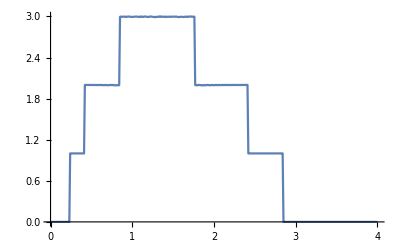

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],(*RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],*)Table[imp,36]]]
```

{imp,imp7,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp11,imp12,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp14,imp,imp3,imp,imp,imp,imp,imp,imp8,imp,imp13,imp,imp,imp10,imp6,imp,imp,imp,imp,imp9,imp4}

```mathematica
m2[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp5,imp1,imp8,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp6,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp14,imp9,imp11,imp,imp,imp,imp,imp2,imp3,imp,imp,imp,imp,imp,imp,imp,imp7,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/2imp.dat",%1]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/2imp.dat

```mathematica
Table[{ω,Mean[Table[m2[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.704632987975527*^-7},{0.01,2.496044184440978*^-7},{0.02,2.557841543968845*^-7},{0.03,2.6347247118062706*^-7},{0.04,2.7066763477532607*^-7},{0.05,2.8033745228360786*^-7},{0.06,2.9124575824169284*^-7},{0.07,3.0428475294241204*^-7},{0.08,3.17672806368838*^-7},{0.09,3.355694693024892*^-7},{0.1,3.564057785074913*^-7},{0.11,3.8766789378651706*^-7},{0.12,4.2360930445810663*^-7},{0.13,4.722121908921817*^-7},{0.14,5.412331142668141*^-7},{0.15,6.309048550207456*^-7},{0.16,7.533145048760347*^-7},{0.17,9.272487559681996*^-7},{0.18,1.2006819171467147*^-6},{0.19,1.6589092873859125*^-6},{0.2,2.515826923097029*^-6},{0.21,4.57796031517402*^-6},{0.22,0.000011773774549179057},{0.23,0.00010160236188442353},{0.24,0.10410123690981363},{0.25,0.40365541172022923},{0.26,0.5792694423069693},{0.27,0.6785981886020643},{0.28,0.7331537483518545},{0.29,0.7637262148805901},{0.3,0.7856241646994478},{0.31,0.799485960223548},{0.32,0.813607460139711},{0.33,0.827476730914698},{0.34,0.8315000501829243},{0.35000000000000003,0.8397368828524636},{0.36,0.8426480553208271},{0.37,0.846041740972624},{0.38,0.8449841155723324},{0.39,0.8422158424256451},{0.4,0.8236635553529235},{0.41000000000000003,0.7310075548781498},{0.42,0.7272510892204159},{0.43,0.7442842715578489},{0.44,0.8525775198882811},{0.45,1.0086761292815236},{0.46,1.1484736773231052},{0.47000000000000003,1.2456024617277353},{0.48,1.3188924736797378},{0.49,1.3608875342181326},{0.5,1.42464129283685},{0.51,1.460070582008324},{0.52,1.4809525677149817},{0.53,1.5002433659998822},{0.54,1.519341665170146},{0.55,1.5470616121188778},{0.56,1.5602608258485122},{0.5700000000000001,1.574759868227213},{0.58,1.5937127754928064},{0.59,1.590357288185235},{0.6,1.6043916524150996},{0.61,1.616484420712905},{0.62,1.6272463452326074},{0.63,1.6292200546126387},{0.64,1.6407555798818565},{0.65,1.6447649455894333},{0.66,1.657428799934087},{0.67,1.6597472435080052},{0.68,1.6519301273627924},{0.6900000000000001,1.6691589576815482},{0.7000000000000001,1.6708533707188622},{0.71,1.6761670952149372},{0.72,1.6765395269493366},{0.73,1.6851141885350716},{0.74,1.6951356588346855},{0.75,1.6914395030555216},{0.76,1.6956888304152522},{0.77,1.6946062902134296},{0.78,1.7068712734942268},{0.79,1.706632741245019},{0.8,1.7174062721182197},{0.81,1.7150196184195798},{0.8200000000000001,1.711615380446941},{0.8300000000000001,1.704086829375836},{0.84,1.6566061479084884},{0.85,0.9761815118235782},{0.86,0.9712387778305647},{0.87,1.1759596723219508},{0.88,1.4656007556012427},{0.89,1.674610648721279},{0.9,1.7647070971292032},{0.91,1.9213382769484333},{0.92,2.0070540808972592},{0.93,2.0770868271850467},{0.9400000000000001,2.1358397060409255},{0.9500000000000001,2.182076370471657},{0.96,2.227799825386289},{0.97,2.279680883290939},{0.98,2.324046956993979},{0.99,2.350392332965311},{1.,2.3840802932326826},{1.01,2.4063353561485847},{1.02,2.355200315362462},{1.03,2.1714173271186583},{1.04,1.7314583364176193},{1.05,0.8932794820716088},{1.06,0.3762697566499047},{1.07,0.38221880478419723},{1.08,0.6030059618228466},{1.09,0.9343519636306067},{1.1,1.185742128663515},{1.11,1.3423165417217788},{1.12,1.4770263510602846},{1.1300000000000001,1.5770342068013135},{1.1400000000000001,1.6590604208009805},{1.1500000000000001,1.7060401795348807},{1.16,1.7842567715953714},{1.17,1.8003304114361076},{1.18,1.861165078604225},{1.19,1.8751373412617833},{1.2,1.9032246595229276},{1.21,1.9181377975393896},{1.22,1.9344980842676855},{1.23,1.9572073022048102},{1.24,1.9314965156108037},{1.25,1.961079996238339},{1.26,1.9798603962319117},{1.27,1.9657826179892723},{1.28,1.9760681842026575},{1.29,1.9686716590690156},{1.3,1.98038231170231},{1.31,1.9882860616678346},{1.32,1.980362116021196},{1.33,2.003290163407066},{1.34,1.9699835247119473},{1.35,2.0015950023991183},{1.36,2.001207371773132},{1.37,2.0072415861718182},{1.3800000000000001,2.002082178084792},{1.3900000000000001,1.9666871802689927},{1.4000000000000001,1.9766592221922206},{1.41,1.9808055042391797},{1.42,1.956510656716693},{1.43,1.966220424155203},{1.44,1.9580893146893201},{1.45,1.930740873795531},{1.46,1.923677678197954},{1.47,1.9462374676497416},{1.48,1.9351596070112802},{1.49,1.9211195288398772},{1.5,1.9256408127588882},{1.51,1.906905580410717},{1.52,1.882992707687079},{1.53,1.874737979492471},{1.54,1.860798043743741},{1.55,1.8409479931468982},{1.56,1.810664463777698},{1.57,1.7911066953586336},{1.58,1.7604175272014535},{1.59,1.742153221684609},{1.6,1.7092307332667105},{1.61,1.6921325075651354},{1.62,1.653596174787107},{1.6300000000000001,1.6406065067689297},{1.6400000000000001,1.6316167403064434},{1.6500000000000001,1.5975594933859447},{1.6600000000000001,1.5249762510576},{1.67,1.4481949685956277},{1.68,1.405651029422473},{1.69,1.3919703456015988},{1.7,1.2445592191320083},{1.71,1.1942558605560551},{1.72,1.0403693293680933},{1.73,0.9433288259369212},{1.74,0.8414354780096355},{1.75,0.8106995164374091},{1.76,1.1473035451116411},{1.77,1.0951350555901387},{1.78,0.9704319522092627},{1.79,0.8672978698898081},{1.8,0.8702535183579814},{1.81,0.9896287918905196},{1.82,1.1423191738542242},{1.83,1.2447607520728616},{1.84,1.3155808786643997},{1.85,1.3510751358150466},{1.86,1.3808730459342464},{1.87,1.4004808603192944},{1.8800000000000001,1.4177488286915307},{1.8900000000000001,1.4310199580917435},{1.9000000000000001,1.433130301694173},{1.9100000000000001,1.444675212497995},{1.92,1.4515016060702057},{1.93,1.4595750747578233},{1.94,1.4556940022994425},{1.95,1.4524361850484393},{1.96,1.4618541205855995},{1.97,1.4547597525011782},{1.98,1.4471179659034041},{1.99,1.4582567499199774},{2.,1.457750379949237},{2.0100000000000002,1.4537366199158865},{2.02,1.4450962114722288},{2.0300000000000002,1.4460085603582968},{2.04,1.4483695125704095},{2.05,1.4332704248854073},{2.06,1.4387090110375544},{2.07,1.4273357884004816},{2.08,1.4284190370982726},{2.09,1.4198954124791918},{2.1,1.4107939669173637},{2.11,1.4063197990862202},{2.12,1.4027383930486896},{2.13,1.381490812804894},{2.14,1.376293422267841},{2.15,1.3660449244107322},{2.16,1.3611531827502805},{2.17,1.3625830782459294},{2.18,1.3456675541027658},{2.19,1.333104592026386},{2.2,1.3159645785566199},{2.21,1.3081229066307958},{2.22,1.2891448386930073},{2.23,1.2781663628283213},{2.24,1.266161446076714},{2.25,1.2447325895919832},{2.2600000000000002,1.2376009682107585},{2.27,1.2149650645449883},{2.2800000000000002,1.1797084797659723},{2.29,1.1684845537896655},{2.3000000000000003,1.13508815258889},{2.31,1.1067460422341215},{2.32,1.0691542711085202},{2.33,1.0438902807780155},{2.34,1.000134817570307},{2.35,0.9484368689339183},{2.36,0.8865271151193393},{2.37,0.8159081506835081},{2.38,0.7301085355641251},{2.39,0.6378701287665677},{2.4,0.5690200221789115},{2.41,0.654654026655794},{2.42,0.5743212104488823},{2.43,0.45848308725019427},{2.44,0.3850025492165045},{2.45,0.4193400080695512},{2.46,0.5195613116209706},{2.47,0.5781614987724776},{2.48,0.6300462089235399},{2.49,0.6614986327757619},{2.5,0.6737288993817256},{2.5100000000000002,0.6823136450293434},{2.52,0.6837900077418483},{2.5300000000000002,0.694891644639446},{2.54,0.6920349499598585},{2.5500000000000003,0.6955188634420411},{2.56,0.6888257633510964},{2.57,0.6925822045765307},{2.58,0.6852928300918931},{2.59,0.6850966489977648},{2.6,0.6846682309074843},{2.61,0.6734677186048722},{2.62,0.670932781651375},{2.63,0.6710613132467637},{2.64,0.6618180314574666},{2.65,0.6526223753312027},{2.66,0.6390605949838059},{2.67,0.6360205195750743},{2.68,0.6262171842186983},{2.69,0.6135497660610378},{2.7,0.6001767595733282},{2.71,0.5838460405758388},{2.72,0.5773059853773356},{2.73,0.5645626938814187},{2.74,0.5388209981103073},{2.75,0.5200124825654211},{2.7600000000000002,0.5093410205310923},{2.77,0.4825622769527476},{2.7800000000000002,0.4507705624025182},{2.79,0.4242734061659729},{2.8000000000000003,0.37065157302965074},{2.81,0.3372837499392245},{2.82,0.2824458986387373},{2.83,0.22660728630332033},{2.84,0.16639059864081177},{2.85,0.00038495050302980336},{2.86,0.00001617013023069728},{2.87,4.866680318412257*^-6},{2.88,2.2924634915756164*^-6},{2.89,1.3111734111260258*^-6},{2.9,8.374352112598765*^-7},{2.91,5.91086253545519*^-7},{2.92,4.3869680543845176*^-7},{2.93,3.413595891428582*^-7},{2.94,2.728212711007632*^-7},{2.95,2.235704844464083*^-7},{2.96,1.8558905260608673*^-7},{2.97,1.551867866131008*^-7},{2.98,1.3169427090272085*^-7},{2.99,1.1289738497374877*^-7},{3.,9.84074212253716*^-8}}
```

{{0.,2.70463×10^-7},{0.01,2.49604×10^-7},{0.02,2.55784×10^-7},{0.03,2.63472×10^-7},{0.04,2.70668×10^-7},{0.05,2.80337×10^-7},{0.06,2.91246×10^-7},{0.07,3.04285×10^-7},{0.08,3.17673×10^-7},{0.09,3.35569×10^-7},{0.1,3.56406×10^-7},{0.11,3.87668×10^-7},{0.12,4.23609×10^-7},{0.13,4.72212×10^-7},{0.14,5.41233×10^-7},{0.15,6.30905×10^-7},{0.16,7.53315×10^-7},{0.17,9.27249×10^-7},{0.18,1.20068×10^-6},{0.19,1.65891×10^-6},{0.2,2.51583×10^-6},{0.21,4.57796×10^-6},{0.22,0.0000117738},{0.23,0.000101602},{0.24,0.104101},{0.25,0.403655},{0.26,0.579269},{0.27,0.678598},{0.28,0.733154},{0.29,0.763726},{0.3,0.785624},{0.31,0.799486},{0.32,0.813607},{0.33,0.827477},{0.34,0.8315},{0.35,0.839737},{0.36,0.842648},{0.37,0.846042},{0.38,0.844984},{0.39,0.842216},{0.4,0.823664},{0.41,0.731008},{0.42,0.727251},{0.43,0.744284},{0.44,0.852578},{0.45,1.00868},{0.46,1.14847},{0.47,1.2456},{0.48,1.31889},{0.49,1.36089},{0.5,1.42464},{0.51,1.46007},{0.52,1.48095},{0.53,1.50024},{0.54,1.51934},{0.55,1.54706},{0.56,1.56026},{0.57,1.57476},{0.58,1.59371},{0.59,1.59036},{0.6,1.60439},{0.61,1.61648},{0.62,1.62725},{0.63,1.62922},{0.64,1.64076},{0.65,1.64476},{0.66,1.65743},{0.67,1.65975},{0.68,1.65193},{0.69,1.66916},{0.7,1.67085},{0.71,1.67617},{0.72,1.67654},{0.73,1.68511},{0.74,1.69514},{0.75,1.69144},{0.76,1.69569},{0.77,1.69461},{0.78,1.70687},{0.79,1.70663},{0.8,1.71741},{0.81,1.71502},{0.82,1.71162},{0.83,1.70409},{0.84,1.65661},{0.85,0.976182},{0.86,0.971239},{0.87,1.17596},{0.88,1.4656},{0.89,1.67461},{0.9,1.76471},{0.91,1.92134},{0.92,2.00705},{0.93,2.07709},{0.94,2.13584},{0.95,2.18208},{0.96,2.2278},{0.97,2.27968},{0.98,2.32405},{0.99,2.35039},{1.,2.38408},{1.01,2.40634},{1.02,2.3552},{1.03,2.17142},{1.04,1.73146},{1.05,0.893279},{1.06,0.37627},{1.07,0.382219},{1.08,0.603006},{1.09,0.934352},{1.1,1.18574},{1.11,1.34232},{1.12,1.47703},{1.13,1.57703},{1.14,1.65906},{1.15,1.70604},{1.16,1.78426},{1.17,1.80033},{1.18,1.86117},{1.19,1.87514},{1.2,1.90322},{1.21,1.91814},{1.22,1.9345},{1.23,1.95721},{1.24,1.9315},{1.25,1.96108},{1.26,1.97986},{1.27,1.96578},{1.28,1.97607},{1.29,1.96867},{1.3,1.98038},{1.31,1.98829},{1.32,1.98036},{1.33,2.00329},{1.34,1.96998},{1.35,2.0016},{1.36,2.00121},{1.37,2.00724},{1.38,2.00208},{1.39,1.96669},{1.4,1.97666},{1.41,1.98081},{1.42,1.95651},{1.43,1.96622},{1.44,1.95809},{1.45,1.93074},{1.46,1.92368},{1.47,1.94624},{1.48,1.93516},{1.49,1.92112},{1.5,1.92564},{1.51,1.90691},{1.52,1.88299},{1.53,1.87474},{1.54,1.8608},{1.55,1.84095},{1.56,1.81066},{1.57,1.79111},{1.58,1.76042},{1.59,1.74215},{1.6,1.70923},{1.61,1.69213},{1.62,1.6536},{1.63,1.64061},{1.64,1.63162},{1.65,1.59756},{1.66,1.52498},{1.67,1.44819},{1.68,1.40565},{1.69,1.39197},{1.7,1.24456},{1.71,1.19426},{1.72,1.04037},{1.73,0.943329},{1.74,0.841435},{1.75,0.8107},{1.76,1.1473},{1.77,1.09514},{1.78,0.970432},{1.79,0.867298},{1.8,0.870254},{1.81,0.989629},{1.82,1.14232},{1.83,1.24476},{1.84,1.31558},{1.85,1.35108},{1.86,1.38087},{1.87,1.40048},{1.88,1.41775},{1.89,1.43102},{1.9,1.43313},{1.91,1.44468},{1.92,1.4515},{1.93,1.45958},{1.94,1.45569},{1.95,1.45244},{1.96,1.46185},{1.97,1.45476},{1.98,1.44712},{1.99,1.45826},{2.,1.45775},{2.01,1.45374},{2.02,1.4451},{2.03,1.44601},{2.04,1.44837},{2.05,1.43327},{2.06,1.43871},{2.07,1.42734},{2.08,1.42842},{2.09,1.4199},{2.1,1.41079},{2.11,1.40632},{2.12,1.40274},{2.13,1.38149},{2.14,1.37629},{2.15,1.36604},{2.16,1.36115},{2.17,1.36258},{2.18,1.34567},{2.19,1.3331},{2.2,1.31596},{2.21,1.30812},{2.22,1.28914},{2.23,1.27817},{2.24,1.26616},{2.25,1.24473},{2.26,1.2376},{2.27,1.21497},{2.28,1.17971},{2.29,1.16848},{2.3,1.13509},{2.31,1.10675},{2.32,1.06915},{2.33,1.04389},{2.34,1.00013},{2.35,0.948437},{2.36,0.886527},{2.37,0.815908},{2.38,0.730109},{2.39,0.63787},{2.4,0.56902},{2.41,0.654654},{2.42,0.574321},{2.43,0.458483},{2.44,0.385003},{2.45,0.41934},{2.46,0.519561},{2.47,0.578161},{2.48,0.630046},{2.49,0.661499},{2.5,0.673729},{2.51,0.682314},{2.52,0.68379},{2.53,0.694892},{2.54,0.692035},{2.55,0.695519},{2.56,0.688826},{2.57,0.692582},{2.58,0.685293},{2.59,0.685097},{2.6,0.684668},{2.61,0.673468},{2.62,0.670933},{2.63,0.671061},{2.64,0.661818},{2.65,0.652622},{2.66,0.639061},{2.67,0.636021},{2.68,0.626217},{2.69,0.61355},{2.7,0.600177},{2.71,0.583846},{2.72,0.577306},{2.73,0.564563},{2.74,0.538821},{2.75,0.520012},{2.76,0.509341},{2.77,0.482562},{2.78,0.450771},{2.79,0.424273},{2.8,0.370652},{2.81,0.337284},{2.82,0.282446},{2.83,0.226607},{2.84,0.166391},{2.85,0.000384951},{2.86,0.0000161701},{2.87,4.86668×10^-6},{2.88,2.29246×10^-6},{2.89,1.31117×10^-6},{2.9,8.37435×10^-7},{2.91,5.91086×10^-7},{2.92,4.38697×10^-7},{2.93,3.4136×10^-7},{2.94,2.72821×10^-7},{2.95,2.2357×10^-7},{2.96,1.85589×10^-7},{2.97,1.55187×10^-7},{2.98,1.31694×10^-7},{2.99,1.12897×10^-7},{3.,9.84074×10^-8}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},7](*RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],*),Table[imp,29]]]
```

{imp1,imp7,imp,imp14,imp,imp4,imp12,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp11,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp12,imp5,imp6,imp,imp,imp,imp4,imp,imp9,imp,imp,imp8,imp2,imp2,imp7,imp,imp1,imp10,imp,imp6,imp,imp13}

```mathematica
m3[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp,imp,imp,imp4,imp11,imp7,imp6,imp,imp11,imp,imp,imp,imp10,imp2,imp,imp,imp,imp6,imp,imp5,imp,imp14,imp,imp8,imp7,imp,imp2,imp,imp,imp5,imp,imp,imp,imp14,imp13,imp,imp,imp,imp,imp,imp3,imp,imp,imp,imp,imp,imp9,imp13,imp12}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m3[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.6479483140403824*^-7},{0.01,2.430803332805782*^-7},{0.02,2.5144890346084234*^-7},{0.03,2.61824428416448*^-7},{0.04,2.7079772709052186*^-7},{0.05,2.7992114122789383*^-7},{0.06,2.9350663944260867*^-7},{0.07,3.042804123118102*^-7},{0.08,3.204222703162767*^-7},{0.09,3.396670866603802*^-7},{0.1,3.6260844694619956*^-7},{0.11,3.949106933536055*^-7},{0.12,4.3280144322543676*^-7},{0.13,4.824360612541231*^-7},{0.14,5.49256746934322*^-7},{0.15,6.408423866863446*^-7},{0.16,7.635493788698597*^-7},{0.17,9.410242483093902*^-7},{0.18,1.2176469340605489*^-6},{0.19,1.6995849317246122*^-6},{0.2,2.5941479060553466*^-6},{0.21,4.704927560802325*^-6},{0.22,0.000012223510220150495},{0.23,0.00010841723802016615},{0.24,0.06803222942103275},{0.25,0.2248961103103496},{0.26,0.4415876831663595},{0.27,0.5663551501984527},{0.28,0.6389188792414136},{0.29,0.6772033162190337},{0.3,0.7091517337154551},{0.31,0.7276310812044344},{0.32,0.7497157698990837},{0.33,0.7556537102897467},{0.34,0.7724677639306444},{0.35000000000000003,0.7787750405692953},{0.36,0.7830166116599633},{0.37,0.7801031546597453},{0.38,0.7820970597973882},{0.39,0.7729932502965698},{0.4,0.7528165383911993},{0.41000000000000003,0.6577640115510485},{0.42,0.6087290134794682},{0.43,0.7498325896221606},{0.44,0.7120647803117681},{0.45,0.8070741384703819},{0.46,0.9041403944199916},{0.47000000000000003,1.007177821079464},{0.48,1.0985446366679976},{0.49,1.1533102853102994},{0.5,1.2165326204995002},{0.51,1.2728599814810342},{0.52,1.2943717980212717},{0.53,1.328733337458663},{0.54,1.3504794369177153},{0.55,1.3851610291634255},{0.56,1.4098333108233014},{0.5700000000000001,1.423231090539397},{0.58,1.4442501951709221},{0.59,1.4328178260409654},{0.6,1.456157759184956},{0.61,1.480626356752501},{0.62,1.482974085341396},{0.63,1.4855748063003011},{0.64,1.5087526804915266},{0.65,1.5149867057165938},{0.66,1.52363113549985},{0.67,1.5264820564239885},{0.68,1.5311562845888422},{0.6900000000000001,1.5393739959765345},{0.7000000000000001,1.5403347723993004},{0.71,1.5533856468293195},{0.72,1.559138964454938},{0.73,1.566560185935359},{0.74,1.5771173622879475},{0.75,1.573203356887794},{0.76,1.584273833521305},{0.77,1.5812399006154205},{0.78,1.5942124819911327},{0.79,1.5981638848579265},{0.8,1.604154460121205},{0.81,1.597561818790372},{0.8200000000000001,1.5883923499412649},{0.8300000000000001,1.579688471391372},{0.84,1.514257951189418},{0.85,0.9960811759056546},{0.86,0.9252054634632332},{0.87,0.922017555705043},{0.88,1.104814821957992},{0.89,1.2903184973199153},{0.9,1.4333836104432875},{0.91,1.5763354831389111},{0.92,1.6758988501984042},{0.93,1.7881114074386386},{0.9400000000000001,1.8526016830536292},{0.9500000000000001,1.9201652102503155},{0.96,1.9690471039629436},{0.97,2.0312999872767135},{0.98,2.0929884356167174},{0.99,2.1165754423094114},{1.,2.168311986150998},{1.01,2.2245690108093275},{1.02,2.120115006415986},{1.03,1.914829555995625},{1.04,1.4020226235239173},{1.05,0.6255069603632261},{1.06,0.33817482698951384},{1.07,0.3304781189221617},{1.08,0.4190103122818943},{1.09,0.6284918814315782},{1.1,0.8429453458664737},{1.11,1.0021485249979696},{1.12,1.1251761702745466},{1.1300000000000001,1.2370141541808852},{1.1400000000000001,1.317146683760463},{1.1500000000000001,1.3754390243278205},{1.16,1.4543075639519591},{1.17,1.497399201358431},{1.18,1.5384033496640144},{1.19,1.5588213125240693},{1.2,1.5978980032407617},{1.21,1.6189912678511205},{1.22,1.6448633102486323},{1.23,1.6648134295056647},{1.24,1.6418070065591182},{1.25,1.6848133595394248},{1.26,1.6964239505648333},{1.27,1.6425757976976099},{1.28,1.6398071825407068},{1.29,1.6492032429854122},{1.3,1.682899219436},{1.31,1.6824285868538218},{1.32,1.6621947871521912},{1.33,1.7064384910506665},{1.34,1.6759011481479238},{1.35,1.7049757971466684},{1.36,1.7112626582893333},{1.37,1.7122759092148256},{1.3800000000000001,1.7058811304607637},{1.3900000000000001,1.6740308888282056},{1.4000000000000001,1.6781076121808314},{1.41,1.687937576933747},{1.42,1.6632164176241486},{1.43,1.6739047385261414},{1.44,1.6662191143273268},{1.45,1.5954423185249542},{1.46,1.5495996251376067},{1.47,1.5935663655090262},{1.48,1.6182348430411744},{1.49,1.616870313129435},{1.5,1.6151982883578722},{1.51,1.5959718805531784},{1.52,1.5922776331002007},{1.53,1.5695041192374206},{1.54,1.5631126409254126},{1.55,1.5276357784226264},{1.56,1.451501488688276},{1.57,1.386655063917739},{1.58,1.406870637083804},{1.59,1.400477701586474},{1.6,1.3758915637056262},{1.61,1.3485438029102903},{1.62,1.3335885181719072},{1.6300000000000001,1.3081646574751609},{1.6400000000000001,1.2993344318565467},{1.6500000000000001,1.253438939486664},{1.6600000000000001,1.1883764299085917},{1.67,1.0990344138386177},{1.68,1.0710299697631263},{1.69,1.0443485469526204},{1.7,0.9025214403965545},{1.71,0.8908698910576183},{1.72,0.7655021406006213},{1.73,0.7071039205838094},{1.74,0.7066730761589319},{1.75,0.8479087689263873},{1.76,1.3693773206365596},{1.77,1.2237451269339867},{1.78,1.0549058834452345},{1.79,0.906338110398273},{1.8,0.7835468283998938},{1.81,0.7642013599459954},{1.82,0.8481748946447196},{1.83,0.9751295948828731},{1.84,1.0783063451398684},{1.85,1.140393154355827},{1.86,1.187491158154492},{1.87,1.212297432186735},{1.8800000000000001,1.2399566433571523},{1.8900000000000001,1.253633904597956},{1.9000000000000001,1.2464339916763276},{1.9100000000000001,1.2052148449049218},{1.92,1.1912046182625018},{1.93,1.2123008167795952},{1.94,1.2530568668701958},{1.95,1.2662211075965324},{1.96,1.2745132304351094},{1.97,1.2695396565877743},{1.98,1.2740734605770485},{1.99,1.2765697011465915},{2.,1.2862811032486745},{2.0100000000000002,1.268106822209372},{2.02,1.264604118987331},{2.0300000000000002,1.2649356613370468},{2.04,1.265299814735509},{2.05,1.2543668211865893},{2.06,1.2609789133605072},{2.07,1.2526481525278121},{2.08,1.239285670316439},{2.09,1.241457561844457},{2.1,1.2093509655805594},{2.11,1.1774864622815917},{2.12,1.1673427807630934},{2.13,1.1691949414940477},{2.14,1.1805018865153563},{2.15,1.1680033188772692},{2.16,1.1705035725083803},{2.17,1.1650150238128296},{2.18,1.1509183979495035},{2.19,1.1375128291642416},{2.2,1.1189719838798569},{2.21,1.1190825209601283},{2.22,1.086770429110502},{2.23,1.081325924797424},{2.24,1.07391756129251},{2.25,1.0543430842394916},{2.2600000000000002,1.038300573270189},{2.27,1.0032023717207423},{2.2800000000000002,0.9863334082730444},{2.29,0.965191469214942},{2.3000000000000003,0.9429533043473173},{2.31,0.8988748797442632},{2.32,0.8755082993235361},{2.33,0.8438388646429247},{2.34,0.7936152225894714},{2.35,0.7458649764365963},{2.36,0.6840990005103705},{2.37,0.6372037641775526},{2.38,0.5747343850326864},{2.39,0.521558329360948},{2.4,0.5048395290558249},{2.41,0.723271233268581},{2.42,0.6098974253561484},{2.43,0.5170689811093214},{2.44,0.3954646371481081},{2.45,0.3531112801043231},{2.46,0.3802527155930031},{2.47,0.4445535511288011},{2.48,0.5090334862840745},{2.49,0.5463883148030361},{2.5,0.5650370063417768},{2.5100000000000002,0.5822749375280267},{2.52,0.5873318929846492},{2.5300000000000002,0.5977516064347198},{2.54,0.6018914843847276},{2.5500000000000003,0.60607803958846},{2.56,0.609888775174777},{2.57,0.6019981261465209},{2.58,0.6032562346772208},{2.59,0.596804143880376},{2.6,0.5858160965857957},{2.61,0.5920516905075036},{2.62,0.590698776581356},{2.63,0.578123145097984},{2.64,0.5761613152098066},{2.65,0.5588501347330126},{2.66,0.5570397952949637},{2.67,0.5394893968948693},{2.68,0.5340241660621777},{2.69,0.5286318564771821},{2.7,0.5177192611242836},{2.71,0.5027383973852432},{2.72,0.49521609770379754},{2.73,0.47717229248686505},{2.74,0.46081556887267194},{2.75,0.4409339427956779},{2.7600000000000002,0.42718591932357247},{2.77,0.39541330295492516},{2.7800000000000002,0.3734265172451198},{2.79,0.3422296119324525},{2.8000000000000003,0.31079931391983723},{2.81,0.27922013981981375},{2.82,0.2331893844178053},{2.83,0.19586302042041723},{2.84,0.15647464741632228},{2.85,0.00039632376696773977},{2.86,0.000016140825820364784},{2.87,4.874939615149796*^-6},{2.88,2.2868772358381334*^-6},{2.89,1.3131327462865559*^-6},{2.9,8.377598620989048*^-7},{2.91,5.877210698996738*^-7},{2.92,4.3550012001104*^-7},{2.93,3.3909938863581365*^-7},{2.94,2.7083126009490413*^-7},{2.95,2.2152713787472276*^-7},{2.96,1.8493130245810929*^-7},{2.97,1.5433926765071565*^-7},{2.98,1.3036686565872893*^-7},{2.99,1.1196085665564044*^-7},{3.,9.821300419783669*^-8}}
```

{{0.,2.64795×10^-7},{0.01,2.4308×10^-7},{0.02,2.51449×10^-7},{0.03,2.61824×10^-7},{0.04,2.70798×10^-7},{0.05,2.79921×10^-7},{0.06,2.93507×10^-7},{0.07,3.0428×10^-7},{0.08,3.20422×10^-7},{0.09,3.39667×10^-7},{0.1,3.62608×10^-7},{0.11,3.94911×10^-7},{0.12,4.32801×10^-7},{0.13,4.82436×10^-7},{0.14,5.49257×10^-7},{0.15,6.40842×10^-7},{0.16,7.63549×10^-7},{0.17,9.41024×10^-7},{0.18,1.21765×10^-6},{0.19,1.69958×10^-6},{0.2,2.59415×10^-6},{0.21,4.70493×10^-6},{0.22,0.0000122235},{0.23,0.000108417},{0.24,0.0680322},{0.25,0.224896},{0.26,0.441588},{0.27,0.566355},{0.28,0.638919},{0.29,0.677203},{0.3,0.709152},{0.31,0.727631},{0.32,0.749716},{0.33,0.755654},{0.34,0.772468},{0.35,0.778775},{0.36,0.783017},{0.37,0.780103},{0.38,0.782097},{0.39,0.772993},{0.4,0.752817},{0.41,0.657764},{0.42,0.608729},{0.43,0.749833},{0.44,0.712065},{0.45,0.807074},{0.46,0.90414},{0.47,1.00718},{0.48,1.09854},{0.49,1.15331},{0.5,1.21653},{0.51,1.27286},{0.52,1.29437},{0.53,1.32873},{0.54,1.35048},{0.55,1.38516},{0.56,1.40983},{0.57,1.42323},{0.58,1.44425},{0.59,1.43282},{0.6,1.45616},{0.61,1.48063},{0.62,1.48297},{0.63,1.48557},{0.64,1.50875},{0.65,1.51499},{0.66,1.52363},{0.67,1.52648},{0.68,1.53116},{0.69,1.53937},{0.7,1.54033},{0.71,1.55339},{0.72,1.55914},{0.73,1.56656},{0.74,1.57712},{0.75,1.5732},{0.76,1.58427},{0.77,1.58124},{0.78,1.59421},{0.79,1.59816},{0.8,1.60415},{0.81,1.59756},{0.82,1.58839},{0.83,1.57969},{0.84,1.51426},{0.85,0.996081},{0.86,0.925205},{0.87,0.922018},{0.88,1.10481},{0.89,1.29032},{0.9,1.43338},{0.91,1.57634},{0.92,1.6759},{0.93,1.78811},{0.94,1.8526},{0.95,1.92017},{0.96,1.96905},{0.97,2.0313},{0.98,2.09299},{0.99,2.11658},{1.,2.16831},{1.01,2.22457},{1.02,2.12012},{1.03,1.91483},{1.04,1.40202},{1.05,0.625507},{1.06,0.338175},{1.07,0.330478},{1.08,0.41901},{1.09,0.628492},{1.1,0.842945},{1.11,1.00215},{1.12,1.12518},{1.13,1.23701},{1.14,1.31715},{1.15,1.37544},{1.16,1.45431},{1.17,1.4974},{1.18,1.5384},{1.19,1.55882},{1.2,1.5979},{1.21,1.61899},{1.22,1.64486},{1.23,1.66481},{1.24,1.64181},{1.25,1.68481},{1.26,1.69642},{1.27,1.64258},{1.28,1.63981},{1.29,1.6492},{1.3,1.6829},{1.31,1.68243},{1.32,1.66219},{1.33,1.70644},{1.34,1.6759},{1.35,1.70498},{1.36,1.71126},{1.37,1.71228},{1.38,1.70588},{1.39,1.67403},{1.4,1.67811},{1.41,1.68794},{1.42,1.66322},{1.43,1.6739},{1.44,1.66622},{1.45,1.59544},{1.46,1.5496},{1.47,1.59357},{1.48,1.61823},{1.49,1.61687},{1.5,1.6152},{1.51,1.59597},{1.52,1.59228},{1.53,1.5695},{1.54,1.56311},{1.55,1.52764},{1.56,1.4515},{1.57,1.38666},{1.58,1.40687},{1.59,1.40048},{1.6,1.37589},{1.61,1.34854},{1.62,1.33359},{1.63,1.30816},{1.64,1.29933},{1.65,1.25344},{1.66,1.18838},{1.67,1.09903},{1.68,1.07103},{1.69,1.04435},{1.7,0.902521},{1.71,0.89087},{1.72,0.765502},{1.73,0.707104},{1.74,0.706673},{1.75,0.847909},{1.76,1.36938},{1.77,1.22375},{1.78,1.05491},{1.79,0.906338},{1.8,0.783547},{1.81,0.764201},{1.82,0.848175},{1.83,0.97513},{1.84,1.07831},{1.85,1.14039},{1.86,1.18749},{1.87,1.2123},{1.88,1.23996},{1.89,1.25363},{1.9,1.24643},{1.91,1.20521},{1.92,1.1912},{1.93,1.2123},{1.94,1.25306},{1.95,1.26622},{1.96,1.27451},{1.97,1.26954},{1.98,1.27407},{1.99,1.27657},{2.,1.28628},{2.01,1.26811},{2.02,1.2646},{2.03,1.26494},{2.04,1.2653},{2.05,1.25437},{2.06,1.26098},{2.07,1.25265},{2.08,1.23929},{2.09,1.24146},{2.1,1.20935},{2.11,1.17749},{2.12,1.16734},{2.13,1.16919},{2.14,1.1805},{2.15,1.168},{2.16,1.1705},{2.17,1.16502},{2.18,1.15092},{2.19,1.13751},{2.2,1.11897},{2.21,1.11908},{2.22,1.08677},{2.23,1.08133},{2.24,1.07392},{2.25,1.05434},{2.26,1.0383},{2.27,1.0032},{2.28,0.986333},{2.29,0.965191},{2.3,0.942953},{2.31,0.898875},{2.32,0.875508},{2.33,0.843839},{2.34,0.793615},{2.35,0.745865},{2.36,0.684099},{2.37,0.637204},{2.38,0.574734},{2.39,0.521558},{2.4,0.50484},{2.41,0.723271},{2.42,0.609897},{2.43,0.517069},{2.44,0.395465},{2.45,0.353111},{2.46,0.380253},{2.47,0.444554},{2.48,0.509033},{2.49,0.546388},{2.5,0.565037},{2.51,0.582275},{2.52,0.587332},{2.53,0.597752},{2.54,0.601891},{2.55,0.606078},{2.56,0.609889},{2.57,0.601998},{2.58,0.603256},{2.59,0.596804},{2.6,0.585816},{2.61,0.592052},{2.62,0.590699},{2.63,0.578123},{2.64,0.576161},{2.65,0.55885},{2.66,0.55704},{2.67,0.539489},{2.68,0.534024},{2.69,0.528632},{2.7,0.517719},{2.71,0.502738},{2.72,0.495216},{2.73,0.477172},{2.74,0.460816},{2.75,0.440934},{2.76,0.427186},{2.77,0.395413},{2.78,0.373427},{2.79,0.34223},{2.8,0.310799},{2.81,0.27922},{2.82,0.233189},{2.83,0.195863},{2.84,0.156475},{2.85,0.000396324},{2.86,0.0000161408},{2.87,4.87494×10^-6},{2.88,2.28688×10^-6},{2.89,1.31313×10^-6},{2.9,8.3776×10^-7},{2.91,5.87721×10^-7},{2.92,4.355×10^-7},{2.93,3.39099×10^-7},{2.94,2.70831×10^-7},{2.95,2.21527×10^-7},{2.96,1.84931×10^-7},{2.97,1.54339×10^-7},{2.98,1.30367×10^-7},{2.99,1.11961×10^-7},{3.,9.8213×10^-8}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/3imp.dat",%3]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/3imp.dat

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],Table[imp,22]]]
```

{imp9,imp,imp,imp3,imp4,imp,imp8,imp13,imp11,imp,imp,imp6,imp5,imp,imp,imp2,imp4,imp14,imp,imp,imp1,imp11,imp1,imp6,imp,imp,imp3,imp9,imp2,imp,imp14,imp5,imp7,imp13,imp,imp8,imp,imp,imp,imp12,imp,imp7,imp,imp,imp,imp12,imp10,imp,imp10,imp}

```mathematica
m4[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp4,imp2,imp5,imp,imp,imp6,imp7,imp11,imp1,imp9,imp,imp14,imp,imp13,imp,imp8,imp,imp4,imp,imp,imp,imp1,imp12,imp,imp,imp3,imp,imp12,imp,imp14,imp,imp6,imp9,imp,imp13,imp7,imp10,imp3,imp8,imp10,imp,imp5,imp,imp11,imp,imp,imp,imp2}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m4[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.5679612350473*^-7},{0.01,2.436527018318449*^-7},{0.02,2.5278399619216023*^-7},{0.03,2.655694657830352*^-7},{0.04,2.742963634120309*^-7},{0.05,2.8372810767325067*^-7},{0.06,2.962637515249423*^-7},{0.07,3.096398436085711*^-7},{0.08,3.2809552138434346*^-7},{0.09,3.463380843989813*^-7},{0.1,3.7288534869069413*^-7},{0.11,4.020745382406889*^-7},{0.12,4.4141092140198673*^-7},{0.13,4.923168995717284*^-7},{0.14,5.620571250799461*^-7},{0.15,6.532086776347938*^-7},{0.16,7.782678453695413*^-7},{0.17,9.576716873541591*^-7},{0.18,1.239713559092333*^-6},{0.19,1.7196392494931313*^-6},{0.2,2.6451810651029987*^-6},{0.21,4.81330033471183*^-6},{0.22,0.000012556053441567845},{0.23,0.00011321956727875627},{0.24,0.06165741470761998},{0.25,0.1271324690551025},{0.26,0.30712363346496907},{0.27,0.46489479127725714},{0.28,0.5495571321552662},{0.29,0.6080089933458311},{0.3,0.6442939485670317},{0.31,0.6722527201930791},{0.32,0.6877607299756344},{0.33,0.706329048504798},{0.34,0.7162507743409653},{0.35000000000000003,0.726027247630566},{0.36,0.728010418730785},{0.37,0.7277715455083349},{0.38,0.7297134891688191},{0.39,0.7152315031279397},{0.4,0.6908692988575523},{0.41000000000000003,0.6072441699406752},{0.42,0.5599717397787665},{0.43,0.7182945948151277},{0.44,0.6849112015689198},{0.45,0.7120646600593669},{0.46,0.7698378607520442},{0.47000000000000003,0.845316050516081},{0.48,0.9386886915020252},{0.49,0.9794883973040273},{0.5,1.0452407741117244},{0.51,1.1113686364167674},{0.52,1.142350706648227},{0.53,1.1818900611900274},{0.54,1.2021987226536857},{0.55,1.2453393649008906},{0.56,1.2622598757952277},{0.5700000000000001,1.2947565481826178},{0.58,1.3169138123405897},{0.59,1.3155216413863686},{0.6,1.338413521324111},{0.61,1.366626703217468},{0.62,1.3621752932916824},{0.63,1.3663383187395053},{0.64,1.383780021679422},{0.65,1.397037387442616},{0.66,1.4165835323666556},{0.67,1.4210712942195922},{0.68,1.4272999949987102},{0.6900000000000001,1.4355408958616633},{0.7000000000000001,1.4298464874179544},{0.71,1.440662590533046},{0.72,1.4473336315506904},{0.73,1.4611854608244712},{0.74,1.4756859515436171},{0.75,1.4732131016317802},{0.76,1.4703635498702965},{0.77,1.4772660376842768},{0.78,1.488692833662369},{0.79,1.4932792848258425},{0.8,1.5076150146369798},{0.81,1.496237815815866},{0.8200000000000001,1.48825182074869},{0.8300000000000001,1.4695976712608867},{0.84,1.3976211653195212},{0.85,0.9741948306488533},{0.86,0.8944515874849238},{0.87,0.8208777916170202},{0.88,0.8924595784566682},{0.89,1.0417974390914637},{0.9,1.159777925777893},{0.91,1.3247911225106455},{0.92,1.4286280131831453},{0.93,1.5249703504698342},{0.9400000000000001,1.6069913572851948},{0.9500000000000001,1.6896186952016259},{0.96,1.756107742943343},{0.97,1.8346201995708704},{0.98,1.9041416989842923},{0.99,1.912700734320512},{1.,1.9858923792621546},{1.01,2.039154489869294},{1.02,1.955547371353914},{1.03,1.7001074474277902},{1.04,1.1776673427286124},{1.05,0.4894496613731866},{1.06,0.3311773005672663},{1.07,0.33821654895451336},{1.08,0.35864001284686986},{1.09,0.4571930282528234},{1.1,0.6204868085568025},{1.11,0.76205647941948},{1.12,0.8919736976199883},{1.1300000000000001,0.9933616266245221},{1.1400000000000001,1.0563348983462248},{1.1500000000000001,1.1377995610578604},{1.16,1.2140793562621244},{1.17,1.2451983925549877},{1.18,1.2883789236775278},{1.19,1.314111620803465},{1.2,1.3577611936572116},{1.21,1.3817086272537755},{1.22,1.4238602159981597},{1.23,1.4367961586689102},{1.24,1.3974743601537716},{1.25,1.448710776393539},{1.26,1.4614684124846997},{1.27,1.4145902294475021},{1.28,1.4030058782141988},{1.29,1.3969362781261634},{1.3,1.436234568120689},{1.31,1.4413474359319616},{1.32,1.436641089918994},{1.33,1.47340943956501},{1.34,1.4389861908229917},{1.35,1.4711608086916794},{1.36,1.47347577050524},{1.37,1.4804828482199475},{1.3800000000000001,1.4794105702160152},{1.3900000000000001,1.4453370529040526},{1.4000000000000001,1.4439631303988631},{1.41,1.4535185543905769},{1.42,1.4255090615099693},{1.43,1.4374459034478633},{1.44,1.4287945975016143},{1.45,1.3772136033890439},{1.46,1.2933986147010919},{1.47,1.3252046109024769},{1.48,1.3573919039310054},{1.49,1.373989423850917},{1.5,1.3729424382712954},{1.51,1.3633289689724144},{1.52,1.3417295542579546},{1.53,1.3363174324860447},{1.54,1.3222762917175321},{1.55,1.298706633195899},{1.56,1.231257368775461},{1.57,1.136397883853394},{1.58,1.1100164087992226},{1.59,1.1195124970275343},{1.6,1.1113166148908102},{1.61,1.1085075482939044},{1.62,1.0836391888191197},{1.6300000000000001,1.0592701342237534},{1.6400000000000001,1.0505657376856927},{1.6500000000000001,1.006053654103767},{1.6600000000000001,0.9394480347524643},{1.67,0.8591029450600551},{1.68,0.8349523055193215},{1.69,0.8177951081863097},{1.7,0.7215873716507331},{1.71,0.6974655490132645},{1.72,0.6454502165828345},{1.73,0.6209150445859631},{1.74,0.6441392087386578},{1.75,0.9326400778193115},{1.76,1.5495342480860512},{1.77,1.3383209431556264},{1.78,1.1750672948571788},{1.79,1.0089165674571157},{1.8,0.7754607184965661},{1.81,0.6802504944317916},{1.82,0.6733951626309375},{1.83,0.7633766877816819},{1.84,0.8750184265061316},{1.85,0.9645840757069543},{1.86,1.0154733435423953},{1.87,1.0425406295078754},{1.8800000000000001,1.0776206073023988},{1.8900000000000001,1.0985776486180538},{1.9000000000000001,1.1046586476412625},{1.9100000000000001,1.070766270862337},{1.92,1.0197173823025718},{1.93,1.0059496279358386},{1.94,1.0720529545449096},{1.95,1.1190250214867141},{1.96,1.1233931516543503},{1.97,1.1233686811478916},{1.98,1.124891119031237},{1.99,1.1274021743613054},{2.,1.1360207947805172},{2.0100000000000002,1.1370877439409426},{2.02,1.1224393780363018},{2.0300000000000002,1.1252051386393165},{2.04,1.1225782252318486},{2.05,1.1116979438335488},{2.06,1.1212747290262883},{2.07,1.1194890128330677},{2.08,1.1012637132583114},{2.09,1.0964743190833068},{2.1,1.0655101573807795},{2.11,1.0377872939287187},{2.12,1.0175213643943415},{2.13,0.9891146373921367},{2.14,1.0021703360422547},{2.15,1.0176259501100478},{2.16,1.0156331887850605},{2.17,1.0052773073101373},{2.18,1.0006655417466144},{2.19,0.9891169368379503},{2.2,0.9720713549788748},{2.21,0.9691900410126958},{2.22,0.9441686301815684},{2.23,0.927012071052267},{2.24,0.9223663724872604},{2.25,0.9003756661239929},{2.2600000000000002,0.8874083438304231},{2.27,0.854477222165983},{2.2800000000000002,0.8305544426195655},{2.29,0.8144564849036104},{2.3000000000000003,0.7901072732304049},{2.31,0.758171358593378},{2.32,0.7337506807277443},{2.33,0.6879898025828273},{2.34,0.6534176663682921},{2.35,0.6129662793238054},{2.36,0.5709253736751103},{2.37,0.5314547112277817},{2.38,0.48451209187065547},{2.39,0.46841437287400384},{2.4,0.5004763903160142},{2.41,0.7822359342197898},{2.42,0.6242436455576708},{2.43,0.5664660418627595},{2.44,0.47390678124697705},{2.45,0.3585972394398675},{2.46,0.3262085955656288},{2.47,0.35390258501996935},{2.48,0.41042646601417543},{2.49,0.4528261321307883},{2.5,0.48913235808299005},{2.5100000000000002,0.49983406815171555},{2.52,0.5120242100093475},{2.5300000000000002,0.522142648826996},{2.54,0.526518733607628},{2.5500000000000003,0.5305563141643025},{2.56,0.5292325085385694},{2.57,0.5350747136528957},{2.58,0.5292350278370557},{2.59,0.5301884448840167},{2.6,0.5182262730511157},{2.61,0.5225495443887141},{2.62,0.5127050479551526},{2.63,0.504576807795735},{2.64,0.5096341635133098},{2.65,0.502768727724209},{2.66,0.49094224769501965},{2.67,0.4856225111323286},{2.68,0.4791334732916706},{2.69,0.46626941522950194},{2.7,0.46137811623003233},{2.71,0.4515595332786561},{2.72,0.4426210471068751},{2.73,0.41735717809377765},{2.74,0.40208187691509206},{2.75,0.38301303609474324},{2.7600000000000002,0.38087930111627893},{2.77,0.3539213206928011},{2.7800000000000002,0.33032196641938966},{2.79,0.29839448079123093},{2.8000000000000003,0.2794449534825476},{2.81,0.23998965601101344},{2.82,0.21595643618775007},{2.83,0.1905252963894285},{2.84,0.1594321034198653},{2.85,0.0004114574321527352},{2.86,0.000016154873835212822},{2.87,4.891470329523554*^-6},{2.88,2.2955556401360624*^-6},{2.89,1.3160455692601403*^-6},{2.9,8.353417611192557*^-7},{2.91,5.864168028770313*^-7},{2.92,4.3582563189362425*^-7},{2.93,3.3953389350126913*^-7},{2.94,2.718280342643585*^-7},{2.95,2.2192663519737615*^-7},{2.96,1.8492843758665451*^-7},{2.97,1.5458763236362174*^-7},{2.98,1.307201904953636*^-7},{2.99,1.1166577344603245*^-7},{3.,9.771626416470072*^-8}}
```

{{0.,2.56796×10^-7},{0.01,2.43653×10^-7},{0.02,2.52784×10^-7},{0.03,2.65569×10^-7},{0.04,2.74296×10^-7},{0.05,2.83728×10^-7},{0.06,2.96264×10^-7},{0.07,3.0964×10^-7},{0.08,3.28096×10^-7},{0.09,3.46338×10^-7},{0.1,3.72885×10^-7},{0.11,4.02075×10^-7},{0.12,4.41411×10^-7},{0.13,4.92317×10^-7},{0.14,5.62057×10^-7},{0.15,6.53209×10^-7},{0.16,7.78268×10^-7},{0.17,9.57672×10^-7},{0.18,1.23971×10^-6},{0.19,1.71964×10^-6},{0.2,2.64518×10^-6},{0.21,4.8133×10^-6},{0.22,0.0000125561},{0.23,0.00011322},{0.24,0.0616574},{0.25,0.127132},{0.26,0.307124},{0.27,0.464895},{0.28,0.549557},{0.29,0.608009},{0.3,0.644294},{0.31,0.672253},{0.32,0.687761},{0.33,0.706329},{0.34,0.716251},{0.35,0.726027},{0.36,0.72801},{0.37,0.727772},{0.38,0.729713},{0.39,0.715232},{0.4,0.690869},{0.41,0.607244},{0.42,0.559972},{0.43,0.718295},{0.44,0.684911},{0.45,0.712065},{0.46,0.769838},{0.47,0.845316},{0.48,0.938689},{0.49,0.979488},{0.5,1.04524},{0.51,1.11137},{0.52,1.14235},{0.53,1.18189},{0.54,1.2022},{0.55,1.24534},{0.56,1.26226},{0.57,1.29476},{0.58,1.31691},{0.59,1.31552},{0.6,1.33841},{0.61,1.36663},{0.62,1.36218},{0.63,1.36634},{0.64,1.38378},{0.65,1.39704},{0.66,1.41658},{0.67,1.42107},{0.68,1.4273},{0.69,1.43554},{0.7,1.42985},{0.71,1.44066},{0.72,1.44733},{0.73,1.46119},{0.74,1.47569},{0.75,1.47321},{0.76,1.47036},{0.77,1.47727},{0.78,1.48869},{0.79,1.49328},{0.8,1.50762},{0.81,1.49624},{0.82,1.48825},{0.83,1.4696},{0.84,1.39762},{0.85,0.974195},{0.86,0.894452},{0.87,0.820878},{0.88,0.89246},{0.89,1.0418},{0.9,1.15978},{0.91,1.32479},{0.92,1.42863},{0.93,1.52497},{0.94,1.60699},{0.95,1.68962},{0.96,1.75611},{0.97,1.83462},{0.98,1.90414},{0.99,1.9127},{1.,1.98589},{1.01,2.03915},{1.02,1.95555},{1.03,1.70011},{1.04,1.17767},{1.05,0.48945},{1.06,0.331177},{1.07,0.338217},{1.08,0.35864},{1.09,0.457193},{1.1,0.620487},{1.11,0.762056},{1.12,0.891974},{1.13,0.993362},{1.14,1.05633},{1.15,1.1378},{1.16,1.21408},{1.17,1.2452},{1.18,1.28838},{1.19,1.31411},{1.2,1.35776},{1.21,1.38171},{1.22,1.42386},{1.23,1.4368},{1.24,1.39747},{1.25,1.44871},{1.26,1.46147},{1.27,1.41459},{1.28,1.40301},{1.29,1.39694},{1.3,1.43623},{1.31,1.44135},{1.32,1.43664},{1.33,1.47341},{1.34,1.43899},{1.35,1.47116},{1.36,1.47348},{1.37,1.48048},{1.38,1.47941},{1.39,1.44534},{1.4,1.44396},{1.41,1.45352},{1.42,1.42551},{1.43,1.43745},{1.44,1.42879},{1.45,1.37721},{1.46,1.2934},{1.47,1.3252},{1.48,1.35739},{1.49,1.37399},{1.5,1.37294},{1.51,1.36333},{1.52,1.34173},{1.53,1.33632},{1.54,1.32228},{1.55,1.29871},{1.56,1.23126},{1.57,1.1364},{1.58,1.11002},{1.59,1.11951},{1.6,1.11132},{1.61,1.10851},{1.62,1.08364},{1.63,1.05927},{1.64,1.05057},{1.65,1.00605},{1.66,0.939448},{1.67,0.859103},{1.68,0.834952},{1.69,0.817795},{1.7,0.721587},{1.71,0.697466},{1.72,0.64545},{1.73,0.620915},{1.74,0.644139},{1.75,0.93264},{1.76,1.54953},{1.77,1.33832},{1.78,1.17507},{1.79,1.00892},{1.8,0.775461},{1.81,0.68025},{1.82,0.673395},{1.83,0.763377},{1.84,0.875018},{1.85,0.964584},{1.86,1.01547},{1.87,1.04254},{1.88,1.07762},{1.89,1.09858},{1.9,1.10466},{1.91,1.07077},{1.92,1.01972},{1.93,1.00595},{1.94,1.07205},{1.95,1.11903},{1.96,1.12339},{1.97,1.12337},{1.98,1.12489},{1.99,1.1274},{2.,1.13602},{2.01,1.13709},{2.02,1.12244},{2.03,1.12521},{2.04,1.12258},{2.05,1.1117},{2.06,1.12127},{2.07,1.11949},{2.08,1.10126},{2.09,1.09647},{2.1,1.06551},{2.11,1.03779},{2.12,1.01752},{2.13,0.989115},{2.14,1.00217},{2.15,1.01763},{2.16,1.01563},{2.17,1.00528},{2.18,1.00067},{2.19,0.989117},{2.2,0.972071},{2.21,0.96919},{2.22,0.944169},{2.23,0.927012},{2.24,0.922366},{2.25,0.900376},{2.26,0.887408},{2.27,0.854477},{2.28,0.830554},{2.29,0.814456},{2.3,0.790107},{2.31,0.758171},{2.32,0.733751},{2.33,0.68799},{2.34,0.653418},{2.35,0.612966},{2.36,0.570925},{2.37,0.531455},{2.38,0.484512},{2.39,0.468414},{2.4,0.500476},{2.41,0.782236},{2.42,0.624244},{2.43,0.566466},{2.44,0.473907},{2.45,0.358597},{2.46,0.326209},{2.47,0.353903},{2.48,0.410426},{2.49,0.452826},{2.5,0.489132},{2.51,0.499834},{2.52,0.512024},{2.53,0.522143},{2.54,0.526519},{2.55,0.530556},{2.56,0.529233},{2.57,0.535075},{2.58,0.529235},{2.59,0.530188},{2.6,0.518226},{2.61,0.52255},{2.62,0.512705},{2.63,0.504577},{2.64,0.509634},{2.65,0.502769},{2.66,0.490942},{2.67,0.485623},{2.68,0.479133},{2.69,0.466269},{2.7,0.461378},{2.71,0.45156},{2.72,0.442621},{2.73,0.417357},{2.74,0.402082},{2.75,0.383013},{2.76,0.380879},{2.77,0.353921},{2.78,0.330322},{2.79,0.298394},{2.8,0.279445},{2.81,0.23999},{2.82,0.215956},{2.83,0.190525},{2.84,0.159432},{2.85,0.000411457},{2.86,0.0000161549},{2.87,4.89147×10^-6},{2.88,2.29556×10^-6},{2.89,1.31605×10^-6},{2.9,8.35342×10^-7},{2.91,5.86417×10^-7},{2.92,4.35826×10^-7},{2.93,3.39534×10^-7},{2.94,2.71828×10^-7},{2.95,2.21927×10^-7},{2.96,1.84928×10^-7},{2.97,1.54588×10^-7},{2.98,1.3072×10^-7},{2.99,1.11666×10^-7},{3.,9.77163×10^-8}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/4imp.dat",%5]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/4imp.dat

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},7],Table[imp,15]]]
```

{imp9,imp3,imp5,imp1,imp,imp,imp14,imp13,imp1,imp4,imp7,imp,imp,imp10,imp2,imp12,imp6,imp,imp13,imp4,imp6,imp,imp11,imp1,imp,imp5,imp,imp10,imp2,imp,imp14,imp,imp9,imp12,imp6,imp11,imp,imp,imp3,imp,imp10,imp3,imp8,imp9,imp14,imp12,imp,imp8,imp7,imp}

```mathematica
m5[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp14,imp5,imp5,imp,imp8,imp7,imp10,imp,imp2,imp,imp14,imp,imp12,imp2,imp,imp3,imp,imp1,imp,imp9,imp6,imp10,imp11,imp2,imp4,imp6,imp,imp5,imp12,imp13,imp7,imp,imp14,imp,imp8,imp9,imp,imp1,imp3,imp11,imp13,imp11,imp4,imp,imp,imp9,imp6,imp3,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m5[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.562222451707216*^-7},{0.01,2.450250775932474*^-7},{0.02,2.5835036456051524*^-7},{0.03,2.697271514500551*^-7},{0.04,2.803562128041165*^-7},{0.05,2.8984948526761503*^-7},{0.06,3.010640488140367*^-7},{0.07,3.1581359396130715*^-7},{0.08,3.338816192828263*^-7},{0.09,3.527507478252502*^-7},{0.1,3.7830871098324065*^-7},{0.11,4.104004187467525*^-7},{0.12,4.4935969281377106*^-7},{0.13,5.018680960086972*^-7},{0.14,5.70373107156479*^-7},{0.15,6.617725011608821*^-7},{0.16,7.867450189669288*^-7},{0.17,9.720288583557372*^-7},{0.18,1.2567340628281357*^-6},{0.19,1.7410327448441909*^-6},{0.2,2.6704419092755934*^-6},{0.21,4.875014024228559*^-6},{0.22,0.000012814817066950177},{0.23,0.00011708666523370675},{0.24,0.059913326834406325},{0.25,0.08675077353321259},{0.26,0.2165347220236056},{0.27,0.37548058178502886},{0.28,0.47696505379662724},{0.29,0.5467007702295278},{0.3,0.5979633317394932},{0.31,0.6316582103162385},{0.32,0.6401662786561424},{0.33,0.6631984781331717},{0.34,0.6669477549340873},{0.35000000000000003,0.6804178512417639},{0.36,0.6841048549742762},{0.37,0.6776945599710082},{0.38,0.6810877437283404},{0.39,0.6684532904387718},{0.4,0.6359041832646424},{0.41000000000000003,0.5730802502035574},{0.42,0.5329537383354069},{0.43,0.6229897114480841},{0.44,0.6924461223542259},{0.45,0.6745139006017159},{0.46,0.6941018175697975},{0.47000000000000003,0.7429664400408778},{0.48,0.8098390244923094},{0.49,0.8585241653799733},{0.5,0.9303702862525357},{0.51,0.9921558542653195},{0.52,1.0137977139707839},{0.53,1.0592298113276675},{0.54,1.0845583617661458},{0.55,1.1426807891444664},{0.56,1.1544185172016137},{0.5700000000000001,1.1936671967643926},{0.58,1.2111329665275998},{0.59,1.202473497721228},{0.6,1.2402774017394604},{0.61,1.2644844178052057},{0.62,1.2733624219899902},{0.63,1.28348937311897},{0.64,1.2905702164957853},{0.65,1.3031987237305929},{0.66,1.3169550427007972},{0.67,1.321192382615051},{0.68,1.3264492504298933},{0.6900000000000001,1.33730596815045},{0.7000000000000001,1.3414035644329916},{0.71,1.3522107643980321},{0.72,1.356196972251925},{0.73,1.3640528408948354},{0.74,1.3885882765310706},{0.75,1.3796052363884033},{0.76,1.380398306713962},{0.77,1.3851087040779224},{0.78,1.400379668194353},{0.79,1.4028299013637862},{0.8,1.4133551530594428},{0.81,1.4056589444730094},{0.8200000000000001,1.3826762154332384},{0.8300000000000001,1.3795684692806975},{0.84,1.2843224529686927},{0.85,0.924613039854158},{0.86,0.8696654987441417},{0.87,0.8022156582359978},{0.88,0.8013049328593315},{0.89,0.867115615747135},{0.9,0.9983140207814556},{0.91,1.1184756612922393},{0.92,1.2383259703334264},{0.93,1.343590387474436},{0.9400000000000001,1.440007908535821},{0.9500000000000001,1.4987106384890858},{0.96,1.5844348808995337},{0.97,1.639360183296561},{0.98,1.7317317413888649},{0.99,1.7481376501805959},{1.,1.8250173813111614},{1.01,1.9038877789368123},{1.02,1.803063732973877},{1.03,1.5339061114157402},{1.04,0.9892217393646124},{1.05,0.42706971967120855},{1.06,0.34240882854455695},{1.07,0.3488848823233144},{1.08,0.33451441071035726},{1.09,0.40327291169208057},{1.1,0.5130968428984576},{1.11,0.6211963060465728},{1.12,0.7115049112546138},{1.1300000000000001,0.8165858753992347},{1.1400000000000001,0.8882045749766739},{1.1500000000000001,0.9338409678859232},{1.16,1.0464976356169158},{1.17,1.0645427662196294},{1.18,1.1219060796632148},{1.19,1.135825128875791},{1.2,1.192111461619194},{1.21,1.193175189926241},{1.22,1.2462621082426357},{1.23,1.259948425056844},{1.24,1.2213958447789983},{1.25,1.253144219959674},{1.26,1.267838973902139},{1.27,1.2351639307191085},{1.28,1.2374533644113963},{1.29,1.2138802856959092},{1.3,1.2498163239687121},{1.31,1.2553550386810175},{1.32,1.2491003526945743},{1.33,1.2938959534904888},{1.34,1.2469027209365595},{1.35,1.2847930162734338},{1.36,1.296492761564612},{1.37,1.3034766306527557},{1.3800000000000001,1.2956270346684449},{1.3900000000000001,1.2692210552302945},{1.4000000000000001,1.2751395400006702},{1.41,1.2836431654304152},{1.42,1.2543593367404435},{1.43,1.2658771984674813},{1.44,1.2490218738033039},{1.45,1.1858612927013559},{1.46,1.1038450352035207},{1.47,1.1006927917256804},{1.48,1.1364094414951478},{1.49,1.1649545891309958},{1.5,1.1789944293308718},{1.51,1.164474314345797},{1.52,1.1592050032399341},{1.53,1.1530081016521987},{1.54,1.1339719185828634},{1.55,1.1099325593452574},{1.56,1.0503200010641065},{1.57,0.9322707723370554},{1.58,0.8530507326872261},{1.59,0.8892592153316315},{1.6,0.9032235275148992},{1.61,0.9031995069955814},{1.62,0.8858530509288467},{1.6300000000000001,0.8720853066448802},{1.6400000000000001,0.8539725955500416},{1.6500000000000001,0.8321227787516231},{1.6600000000000001,0.7708927033353753},{1.67,0.7035351528292739},{1.68,0.6760367612212729},{1.69,0.6756553463568484},{1.7,0.605649517599449},{1.71,0.5849429944902541},{1.72,0.5931095757498624},{1.73,0.6040448876867706},{1.74,0.7004989568560978},{1.75,1.0145102458965567},{1.76,1.6651069660348667},{1.77,1.4536317871857214},{1.78,1.2978957634028747},{1.79,1.0969068992899642},{1.8,0.8755809081393627},{1.81,0.7021933866946499},{1.82,0.591143637812356},{1.83,0.6262810484789356},{1.84,0.7123962426799562},{1.85,0.8046489030343562},{1.86,0.8723772228608588},{1.87,0.9097366711120515},{1.8800000000000001,0.9548411237789323},{1.8900000000000001,0.9665453429965176},{1.9000000000000001,0.9814075828544103},{1.9100000000000001,0.9664581840085082},{1.92,0.886287388184681},{1.93,0.8454310361176336},{1.94,0.8662187887814402},{1.95,0.9478013760542408},{1.96,0.9817058805701784},{1.97,0.9895065624765148},{1.98,0.9940091967920666},{1.99,1.0106464016364212},{2.,1.0180443766088974},{2.0100000000000002,1.0124457384191101},{2.02,0.9942667477179381},{2.0300000000000002,1.0016648596702291},{2.04,1.0081982684462685},{2.05,0.9964188678509065},{2.06,1.0013451848395238},{2.07,1.0015756470057593},{2.08,0.982914648890221},{2.09,0.975104552618642},{2.1,0.9633269433261206},{2.11,0.9279266522928652},{2.12,0.8817087049175699},{2.13,0.8310501396950455},{2.14,0.8681026791814861},{2.15,0.8784137337454004},{2.16,0.8947039625648456},{2.17,0.8898579888000506},{2.18,0.8730355327602781},{2.19,0.8629818009187},{2.2,0.8574442936210606},{2.21,0.8520613612828729},{2.22,0.8312461900004546},{2.23,0.8135844899072388},{2.24,0.8075237468322785},{2.25,0.7876084634945894},{2.2600000000000002,0.7808793962325042},{2.27,0.7483317514520249},{2.2800000000000002,0.7298100943764536},{2.29,0.7140024006345909},{2.3000000000000003,0.6847835456082332},{2.31,0.6570942829787716},{2.32,0.615174299272514},{2.33,0.5891913612597148},{2.34,0.573048031857701},{2.35,0.541158780129779},{2.36,0.49858157237603634},{2.37,0.4728583902221377},{2.38,0.4509228479380749},{2.39,0.45568323722031356},{2.4,0.5319126191325977},{2.41,0.825645023184265},{2.42,0.6529741841226374},{2.43,0.5917400748465443},{2.44,0.5022591638265148},{2.45,0.4171399000982648},{2.46,0.32791018294439295},{2.47,0.3090216361463509},{2.48,0.34607557334241923},{2.49,0.38130408593226894},{2.5,0.42270068797931065},{2.5100000000000002,0.4294966588586486},{2.52,0.4472532771439119},{2.5300000000000002,0.4707730064471607},{2.54,0.47811469997145173},{2.5500000000000003,0.4793129744385539},{2.56,0.4793235288600366},{2.57,0.47203271199639985},{2.58,0.47530423415506895},{2.59,0.4833588295766372},{2.6,0.4667778506291077},{2.61,0.48376166417321065},{2.62,0.46874105110811504},{2.63,0.46178981401064856},{2.64,0.460264747953722},{2.65,0.4553242236535804},{2.66,0.4561303506397176},{2.67,0.45330409710671116},{2.68,0.4340211875873539},{2.69,0.43459138845606465},{2.7,0.41837891933399257},{2.71,0.4103653305207536},{2.72,0.40115660551574367},{2.73,0.3865166346821445},{2.74,0.36946875048539013},{2.75,0.3601699697493126},{2.7600000000000002,0.3396011896161882},{2.77,0.32428498119198834},{2.7800000000000002,0.3130482856233174},{2.79,0.28813147727540933},{2.8000000000000003,0.2616226983297443},{2.81,0.2418512601567408},{2.82,0.2135874414218376},{2.83,0.18228519980961772},{2.84,0.16395584594485768},{2.85,0.00041939144584118},{2.86,0.000016254545460683115},{2.87,4.915816621976202*^-6},{2.88,2.320034602738864*^-6},{2.89,1.3311501533056544*^-6},{2.9,8.532184923599713*^-7},{2.91,5.942753745486443*^-7},{2.92,4.394272079304172*^-7},{2.93,3.414766644616426*^-7},{2.94,2.726066989772615*^-7},{2.95,2.2309592077489407*^-7},{2.96,1.8553952775326456*^-7},{2.97,1.554537117503948*^-7},{2.98,1.3150878926884068*^-7},{2.99,1.1297539518370314*^-7},{3.,9.87301763591951*^-8}}
```

{{0.,2.56222×10^-7},{0.01,2.45025×10^-7},{0.02,2.5835×10^-7},{0.03,2.69727×10^-7},{0.04,2.80356×10^-7},{0.05,2.89849×10^-7},{0.06,3.01064×10^-7},{0.07,3.15814×10^-7},{0.08,3.33882×10^-7},{0.09,3.52751×10^-7},{0.1,3.78309×10^-7},{0.11,4.104×10^-7},{0.12,4.4936×10^-7},{0.13,5.01868×10^-7},{0.14,5.70373×10^-7},{0.15,6.61773×10^-7},{0.16,7.86745×10^-7},{0.17,9.72029×10^-7},{0.18,1.25673×10^-6},{0.19,1.74103×10^-6},{0.2,2.67044×10^-6},{0.21,4.87501×10^-6},{0.22,0.0000128148},{0.23,0.000117087},{0.24,0.0599133},{0.25,0.0867508},{0.26,0.216535},{0.27,0.375481},{0.28,0.476965},{0.29,0.546701},{0.3,0.597963},{0.31,0.631658},{0.32,0.640166},{0.33,0.663198},{0.34,0.666948},{0.35,0.680418},{0.36,0.684105},{0.37,0.677695},{0.38,0.681088},{0.39,0.668453},{0.4,0.635904},{0.41,0.57308},{0.42,0.532954},{0.43,0.62299},{0.44,0.692446},{0.45,0.674514},{0.46,0.694102},{0.47,0.742966},{0.48,0.809839},{0.49,0.858524},{0.5,0.93037},{0.51,0.992156},{0.52,1.0138},{0.53,1.05923},{0.54,1.08456},{0.55,1.14268},{0.56,1.15442},{0.57,1.19367},{0.58,1.21113},{0.59,1.20247},{0.6,1.24028},{0.61,1.26448},{0.62,1.27336},{0.63,1.28349},{0.64,1.29057},{0.65,1.3032},{0.66,1.31696},{0.67,1.32119},{0.68,1.32645},{0.69,1.33731},{0.7,1.3414},{0.71,1.35221},{0.72,1.3562},{0.73,1.36405},{0.74,1.38859},{0.75,1.37961},{0.76,1.3804},{0.77,1.38511},{0.78,1.40038},{0.79,1.40283},{0.8,1.41336},{0.81,1.40566},{0.82,1.38268},{0.83,1.37957},{0.84,1.28432},{0.85,0.924613},{0.86,0.869665},{0.87,0.802216},{0.88,0.801305},{0.89,0.867116},{0.9,0.998314},{0.91,1.11848},{0.92,1.23833},{0.93,1.34359},{0.94,1.44001},{0.95,1.49871},{0.96,1.58443},{0.97,1.63936},{0.98,1.73173},{0.99,1.74814},{1.,1.82502},{1.01,1.90389},{1.02,1.80306},{1.03,1.53391},{1.04,0.989222},{1.05,0.42707},{1.06,0.342409},{1.07,0.348885},{1.08,0.334514},{1.09,0.403273},{1.1,0.513097},{1.11,0.621196},{1.12,0.711505},{1.13,0.816586},{1.14,0.888205},{1.15,0.933841},{1.16,1.0465},{1.17,1.06454},{1.18,1.12191},{1.19,1.13583},{1.2,1.19211},{1.21,1.19318},{1.22,1.24626},{1.23,1.25995},{1.24,1.2214},{1.25,1.25314},{1.26,1.26784},{1.27,1.23516},{1.28,1.23745},{1.29,1.21388},{1.3,1.24982},{1.31,1.25536},{1.32,1.2491},{1.33,1.2939},{1.34,1.2469},{1.35,1.28479},{1.36,1.29649},{1.37,1.30348},{1.38,1.29563},{1.39,1.26922},{1.4,1.27514},{1.41,1.28364},{1.42,1.25436},{1.43,1.26588},{1.44,1.24902},{1.45,1.18586},{1.46,1.10385},{1.47,1.10069},{1.48,1.13641},{1.49,1.16495},{1.5,1.17899},{1.51,1.16447},{1.52,1.15921},{1.53,1.15301},{1.54,1.13397},{1.55,1.10993},{1.56,1.05032},{1.57,0.932271},{1.58,0.853051},{1.59,0.889259},{1.6,0.903224},{1.61,0.9032},{1.62,0.885853},{1.63,0.872085},{1.64,0.853973},{1.65,0.832123},{1.66,0.770893},{1.67,0.703535},{1.68,0.676037},{1.69,0.675655},{1.7,0.60565},{1.71,0.584943},{1.72,0.59311},{1.73,0.604045},{1.74,0.700499},{1.75,1.01451},{1.76,1.66511},{1.77,1.45363},{1.78,1.2979},{1.79,1.09691},{1.8,0.875581},{1.81,0.702193},{1.82,0.591144},{1.83,0.626281},{1.84,0.712396},{1.85,0.804649},{1.86,0.872377},{1.87,0.909737},{1.88,0.954841},{1.89,0.966545},{1.9,0.981408},{1.91,0.966458},{1.92,0.886287},{1.93,0.845431},{1.94,0.866219},{1.95,0.947801},{1.96,0.981706},{1.97,0.989507},{1.98,0.994009},{1.99,1.01065},{2.,1.01804},{2.01,1.01245},{2.02,0.994267},{2.03,1.00166},{2.04,1.0082},{2.05,0.996419},{2.06,1.00135},{2.07,1.00158},{2.08,0.982915},{2.09,0.975105},{2.1,0.963327},{2.11,0.927927},{2.12,0.881709},{2.13,0.83105},{2.14,0.868103},{2.15,0.878414},{2.16,0.894704},{2.17,0.889858},{2.18,0.873036},{2.19,0.862982},{2.2,0.857444},{2.21,0.852061},{2.22,0.831246},{2.23,0.813584},{2.24,0.807524},{2.25,0.787608},{2.26,0.780879},{2.27,0.748332},{2.28,0.72981},{2.29,0.714002},{2.3,0.684784},{2.31,0.657094},{2.32,0.615174},{2.33,0.589191},{2.34,0.573048},{2.35,0.541159},{2.36,0.498582},{2.37,0.472858},{2.38,0.450923},{2.39,0.455683},{2.4,0.531913},{2.41,0.825645},{2.42,0.652974},{2.43,0.59174},{2.44,0.502259},{2.45,0.41714},{2.46,0.32791},{2.47,0.309022},{2.48,0.346076},{2.49,0.381304},{2.5,0.422701},{2.51,0.429497},{2.52,0.447253},{2.53,0.470773},{2.54,0.478115},{2.55,0.479313},{2.56,0.479324},{2.57,0.472033},{2.58,0.475304},{2.59,0.483359},{2.6,0.466778},{2.61,0.483762},{2.62,0.468741},{2.63,0.46179},{2.64,0.460265},{2.65,0.455324},{2.66,0.45613},{2.67,0.453304},{2.68,0.434021},{2.69,0.434591},{2.7,0.418379},{2.71,0.410365},{2.72,0.401157},{2.73,0.386517},{2.74,0.369469},{2.75,0.36017},{2.76,0.339601},{2.77,0.324285},{2.78,0.313048},{2.79,0.288131},{2.8,0.261623},{2.81,0.241851},{2.82,0.213587},{2.83,0.182285},{2.84,0.163956},{2.85,0.000419391},{2.86,0.0000162545},{2.87,4.91582×10^-6},{2.88,2.32003×10^-6},{2.89,1.33115×10^-6},{2.9,8.53218×10^-7},{2.91,5.94275×10^-7},{2.92,4.39427×10^-7},{2.93,3.41477×10^-7},{2.94,2.72607×10^-7},{2.95,2.23096×10^-7},{2.96,1.8554×10^-7},{2.97,1.55454×10^-7},{2.98,1.31509×10^-7},{2.99,1.12975×10^-7},{3.,9.87302×10^-8}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/5imp.dat",%7]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/5imp.dat

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,8]]]
```

{imp9,imp4,imp8,imp2,imp8,imp,imp11,imp,imp,imp6,imp2,imp10,imp5,imp9,imp,imp5,imp7,imp1,imp4,imp4,imp13,imp10,imp6,imp13,imp1,imp3,imp11,imp14,imp12,imp11,imp7,imp14,imp10,imp13,imp2,imp14,imp1,imp12,imp3,imp,imp6,imp5,imp9,imp8,imp3,imp,imp12,imp,imp,imp7}

```mathematica
m6[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp8,imp14,imp4,imp3,imp13,imp,imp11,imp12,imp9,imp,imp7,imp4,imp10,imp3,imp14,imp2,imp10,imp,imp14,imp3,imp,imp6,imp13,imp2,imp,imp12,imp9,imp6,imp1,imp5,imp4,imp13,imp6,imp11,imp1,imp2,imp,imp7,imp5,imp12,imp11,imp,imp10,imp,imp1,imp9,imp8,imp8,imp5,imp7}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m6[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.5778768924487443*^-7},{0.01,2.5182226649096317*^-7},{0.02,2.650290069899847*^-7},{0.03,2.771978870224207*^-7},{0.04,2.8546255299515827*^-7},{0.05,2.9418414441310565*^-7},{0.06,3.070647958563996*^-7},{0.07,3.2010756271891717*^-7},{0.08,3.3728144368886194*^-7},{0.09,3.583698314345702*^-7},{0.1,3.83925860815436*^-7},{0.11,4.158803314601819*^-7},{0.12,4.550861234170213*^-7},{0.13,5.076569887959984*^-7},{0.14,5.755087901267702*^-7},{0.15,6.655603362226784*^-7},{0.16,7.915288829422905*^-7},{0.17,9.78152579972923*^-7},{0.18,1.264037986150751*^-6},{0.19,1.7489952289686844*^-6},{0.2,2.690476281416266*^-6},{0.21,4.9147795726410675*^-6},{0.22,0.000012893755307636461},{0.23,0.00011895486756954999},{0.24,0.059679620775240104},{0.25,0.07356471888729288},{0.26,0.14385649000386416},{0.27,0.2896845203614249},{0.28,0.42750168541438865},{0.29,0.505736914026167},{0.3,0.5548407877092829},{0.31,0.5861615346154081},{0.32,0.6009388590504224},{0.33,0.6162425804578615},{0.34,0.6290059379726973},{0.35000000000000003,0.643350040720783},{0.36,0.6455930089547572},{0.37,0.6358088262399894},{0.38,0.6352284897253455},{0.39,0.6282893375533907},{0.4,0.5908388252027958},{0.41000000000000003,0.5442338917783067},{0.42,0.5218807760867223},{0.43,0.570804465800667},{0.44,0.6721340435392815},{0.45,0.6694357356176266},{0.46,0.6417690136993387},{0.47000000000000003,0.6767213903338527},{0.48,0.7186060187136895},{0.49,0.7678515277773058},{0.5,0.8355503548532962},{0.51,0.8926472904429822},{0.52,0.9214975948702441},{0.53,0.9585588749547373},{0.54,0.9838148624003226},{0.55,1.0328216165829895},{0.56,1.0642904372395146},{0.5700000000000001,1.1004012900175655},{0.58,1.118704611187421},{0.59,1.0979484154652095},{0.6,1.1461571078975252},{0.61,1.1780346846385747},{0.62,1.1794117064378566},{0.63,1.1922740454233316},{0.64,1.2077503355963968},{0.65,1.212874002730143},{0.66,1.2345968450848306},{0.67,1.2386552029721691},{0.68,1.2432420770056258},{0.6900000000000001,1.2623341517467561},{0.7000000000000001,1.2606416003339873},{0.71,1.2747002028152297},{0.72,1.2722693270213454},{0.73,1.290075470042366},{0.74,1.306639309549841},{0.75,1.2971947457278357},{0.76,1.305168014248219},{0.77,1.2991257218634613},{0.78,1.3236570558851677},{0.79,1.3203255875753197},{0.8,1.3348936877535273},{0.81,1.317854240115848},{0.8200000000000001,1.3001757931377924},{0.8300000000000001,1.2718283662935044},{0.84,1.2059364265251704},{0.85,0.8985956714792394},{0.86,0.8670147434821323},{0.87,0.8115505205604326},{0.88,0.7706514256863435},{0.89,0.7714252325004698},{0.9,0.8575827084333234},{0.91,0.9638730660836675},{0.92,1.0582720260816132},{0.93,1.2000765432145635},{0.9400000000000001,1.274187542112404},{0.9500000000000001,1.353042097585333},{0.96,1.4413790356069558},{0.97,1.493001102385475},{0.98,1.5857400870929337},{0.99,1.6375740824958749},{1.,1.7021705402300287},{1.01,1.7879237831656742},{1.02,1.686707505009425},{1.03,1.40193473709121},{1.04,0.854682411216153},{1.05,0.39040346194445213},{1.06,0.34194636268977513},{1.07,0.36021731887066555},{1.08,0.336075900739306},{1.09,0.36722342933125796},{1.1,0.4312838242881653},{1.11,0.5124236507284252},{1.12,0.591387008567605},{1.1300000000000001,0.6870418598021233},{1.1400000000000001,0.7660610361457277},{1.1500000000000001,0.7971521710587834},{1.16,0.8857288459559683},{1.17,0.9128757062160675},{1.18,0.9807538386342503},{1.19,0.9929312587496412},{1.2,1.0316957312059627},{1.21,1.049279368921039},{1.22,1.0944517402577978},{1.23,1.1101140812579242},{1.24,1.0787722864075309},{1.25,1.121464758779494},{1.26,1.1435581902789238},{1.27,1.1051235031621778},{1.28,1.086221634494953},{1.29,1.0643453381361314},{1.3,1.1025353429638143},{1.31,1.0953070442970219},{1.32,1.0775783237319057},{1.33,1.1425774202336005},{1.34,1.0796039274400941},{1.35,1.1275526800770044},{1.36,1.1331108556442906},{1.37,1.1626771240880753},{1.3800000000000001,1.155184974937492},{1.3900000000000001,1.1098492873801438},{1.4000000000000001,1.117286199347213},{1.41,1.1271254859738578},{1.42,1.106319173655143},{1.43,1.1145815421153056},{1.44,1.1101844176679145},{1.45,1.0562557923132927},{1.46,0.9791546369610619},{1.47,0.9394011464837081},{1.48,0.9320096381569297},{1.49,0.9883394993662755},{1.5,1.0077198224548594},{1.51,1.0049948345368038},{1.52,0.9969055179632617},{1.53,0.9903147140334303},{1.54,0.9808984735928088},{1.55,0.9602787174351363},{1.56,0.9017747200089496},{1.57,0.8043823036416733},{1.58,0.7149832348224138},{1.59,0.7107277335540451},{1.6,0.7438075232166537},{1.61,0.7468150472233621},{1.62,0.749486061135448},{1.6300000000000001,0.736516247944479},{1.6400000000000001,0.7280388457560579},{1.6500000000000001,0.7028611081867241},{1.6600000000000001,0.6406263176915232},{1.67,0.6062779531322062},{1.68,0.5834981066043667},{1.69,0.5649471655531156},{1.7,0.5474246446903381},{1.71,0.5558243169019148},{1.72,0.6162564385237134},{1.73,0.6356083928119639},{1.74,0.7499861904605413},{1.75,1.1319883585343864},{1.76,1.7459531954814607},{1.77,1.496733730630602},{1.78,1.3777241411843397},{1.79,1.2064794382938124},{1.8,0.9864421554983279},{1.81,0.8140258198464072},{1.82,0.5868486844365104},{1.83,0.5405320716121045},{1.84,0.5720070546054703},{1.85,0.686909171481411},{1.86,0.7372141914322217},{1.87,0.7986823314366757},{1.8800000000000001,0.8312404006088687},{1.8900000000000001,0.8600687773356401},{1.9000000000000001,0.8687213625582395},{1.9100000000000001,0.8692267562607515},{1.92,0.8226478713740712},{1.93,0.7339552540074445},{1.94,0.7014932451873002},{1.95,0.7792903571196061},{1.96,0.8523397824108481},{1.97,0.8710901495079831},{1.98,0.8838219046839942},{1.99,0.8887931002320716},{2.,0.9085782206391716},{2.0100000000000002,0.9120862524492297},{2.02,0.9069161348232879},{2.0300000000000002,0.9032886225251522},{2.04,0.9180776434981729},{2.05,0.8970307548929349},{2.06,0.9080113206563587},{2.07,0.9031126901862722},{2.08,0.886526478315436},{2.09,0.8958320651009769},{2.1,0.8675283663722811},{2.11,0.8391685056834299},{2.12,0.8030624211621775},{2.13,0.7597766851818843},{2.14,0.7384014635370999},{2.15,0.751315142500631},{2.16,0.7748378326273532},{2.17,0.7941651360289825},{2.18,0.7818661137969575},{2.19,0.7672684936649925},{2.2,0.763318978506414},{2.21,0.7596892151896432},{2.22,0.7341444555101974},{2.23,0.7267482471954751},{2.24,0.7186511280195319},{2.25,0.6941894113419028},{2.2600000000000002,0.6913361371866273},{2.27,0.6611154881248863},{2.2800000000000002,0.6478154678695984},{2.29,0.636697358648688},{2.3000000000000003,0.6095646437421708},{2.31,0.5856239273537818},{2.32,0.5641384882397097},{2.33,0.5287310303009792},{2.34,0.5005698650715854},{2.35,0.4837127168144833},{2.36,0.46015782485353646},{2.37,0.4350635633868255},{2.38,0.42222930909729794},{2.39,0.44876719334964105},{2.4,0.5370121348947037},{2.41,0.8767334331842805},{2.42,0.6747938809266497},{2.43,0.621274711243},{2.44,0.5615701837082724},{2.45,0.4816843249121314},{2.46,0.37503164727692384},{2.47,0.3053445607989072},{2.48,0.2977109525670046},{2.49,0.33288028479496573},{2.5,0.3664543233106511},{2.5100000000000002,0.39111389340406605},{2.52,0.4068846645000387},{2.5300000000000002,0.42140415744294524},{2.54,0.4315849243163362},{2.5500000000000003,0.43145543079076165},{2.56,0.4357369367716361},{2.57,0.4330335517324839},{2.58,0.4356940706861234},{2.59,0.43906321925463193},{2.6,0.43813537546091025},{2.61,0.43280591739336804},{2.62,0.4306958295944142},{2.63,0.43867518847696557},{2.64,0.41890023551127875},{2.65,0.42262819425605436},{2.66,0.4226758452085161},{2.67,0.4208712122710324},{2.68,0.41434354181446376},{2.69,0.40532081934420094},{2.7,0.4024851766970784},{2.71,0.3948908621442388},{2.72,0.3823202637921341},{2.73,0.36744963275536313},{2.74,0.35908826145930367},{2.75,0.3480895515374343},{2.7600000000000002,0.33529411888864397},{2.77,0.32295699224686003},{2.7800000000000002,0.3023650874345612},{2.79,0.28515698521338867},{2.8000000000000003,0.2641083964594556},{2.81,0.24810204790333776},{2.82,0.21598885765893555},{2.83,0.2041680820650627},{2.84,0.1836043956983142},{2.85,0.00043705155146381183},{2.86,0.000016338186429464116},{2.87,4.945857153080141*^-6},{2.88,2.3356587478583047*^-6},{2.89,1.3476777881389337*^-6},{2.9,8.687637102108047*^-7},{2.91,6.055725226592366*^-7},{2.92,4.4712999020660364*^-7},{2.93,3.458856303282886*^-7},{2.94,2.755876996102286*^-7},{2.95,2.2471023452668112*^-7},{2.96,1.8655006991999284*^-7},{2.97,1.5675447305874226*^-7},{2.98,1.327742342546085*^-7},{2.99,1.1426486234796676*^-7},{3.,9.948764930953225*^-8}}
```

{{0.,2.57788×10^-7},{0.01,2.51822×10^-7},{0.02,2.65029×10^-7},{0.03,2.77198×10^-7},{0.04,2.85463×10^-7},{0.05,2.94184×10^-7},{0.06,3.07065×10^-7},{0.07,3.20108×10^-7},{0.08,3.37281×10^-7},{0.09,3.5837×10^-7},{0.1,3.83926×10^-7},{0.11,4.1588×10^-7},{0.12,4.55086×10^-7},{0.13,5.07657×10^-7},{0.14,5.75509×10^-7},{0.15,6.6556×10^-7},{0.16,7.91529×10^-7},{0.17,9.78153×10^-7},{0.18,1.26404×10^-6},{0.19,1.749×10^-6},{0.2,2.69048×10^-6},{0.21,4.91478×10^-6},{0.22,0.0000128938},{0.23,0.000118955},{0.24,0.0596796},{0.25,0.0735647},{0.26,0.143856},{0.27,0.289685},{0.28,0.427502},{0.29,0.505737},{0.3,0.554841},{0.31,0.586162},{0.32,0.600939},{0.33,0.616243},{0.34,0.629006},{0.35,0.64335},{0.36,0.645593},{0.37,0.635809},{0.38,0.635228},{0.39,0.628289},{0.4,0.590839},{0.41,0.544234},{0.42,0.521881},{0.43,0.570804},{0.44,0.672134},{0.45,0.669436},{0.46,0.641769},{0.47,0.676721},{0.48,0.718606},{0.49,0.767852},{0.5,0.83555},{0.51,0.892647},{0.52,0.921498},{0.53,0.958559},{0.54,0.983815},{0.55,1.03282},{0.56,1.06429},{0.57,1.1004},{0.58,1.1187},{0.59,1.09795},{0.6,1.14616},{0.61,1.17803},{0.62,1.17941},{0.63,1.19227},{0.64,1.20775},{0.65,1.21287},{0.66,1.2346},{0.67,1.23866},{0.68,1.24324},{0.69,1.26233},{0.7,1.26064},{0.71,1.2747},{0.72,1.27227},{0.73,1.29008},{0.74,1.30664},{0.75,1.29719},{0.76,1.30517},{0.77,1.29913},{0.78,1.32366},{0.79,1.32033},{0.8,1.33489},{0.81,1.31785},{0.82,1.30018},{0.83,1.27183},{0.84,1.20594},{0.85,0.898596},{0.86,0.867015},{0.87,0.811551},{0.88,0.770651},{0.89,0.771425},{0.9,0.857583},{0.91,0.963873},{0.92,1.05827},{0.93,1.20008},{0.94,1.27419},{0.95,1.35304},{0.96,1.44138},{0.97,1.493},{0.98,1.58574},{0.99,1.63757},{1.,1.70217},{1.01,1.78792},{1.02,1.68671},{1.03,1.40193},{1.04,0.854682},{1.05,0.390403},{1.06,0.341946},{1.07,0.360217},{1.08,0.336076},{1.09,0.367223},{1.1,0.431284},{1.11,0.512424},{1.12,0.591387},{1.13,0.687042},{1.14,0.766061},{1.15,0.797152},{1.16,0.885729},{1.17,0.912876},{1.18,0.980754},{1.19,0.992931},{1.2,1.0317},{1.21,1.04928},{1.22,1.09445},{1.23,1.11011},{1.24,1.07877},{1.25,1.12146},{1.26,1.14356},{1.27,1.10512},{1.28,1.08622},{1.29,1.06435},{1.3,1.10254},{1.31,1.09531},{1.32,1.07758},{1.33,1.14258},{1.34,1.0796},{1.35,1.12755},{1.36,1.13311},{1.37,1.16268},{1.38,1.15518},{1.39,1.10985},{1.4,1.11729},{1.41,1.12713},{1.42,1.10632},{1.43,1.11458},{1.44,1.11018},{1.45,1.05626},{1.46,0.979155},{1.47,0.939401},{1.48,0.93201},{1.49,0.988339},{1.5,1.00772},{1.51,1.00499},{1.52,0.996906},{1.53,0.990315},{1.54,0.980898},{1.55,0.960279},{1.56,0.901775},{1.57,0.804382},{1.58,0.714983},{1.59,0.710728},{1.6,0.743808},{1.61,0.746815},{1.62,0.749486},{1.63,0.736516},{1.64,0.728039},{1.65,0.702861},{1.66,0.640626},{1.67,0.606278},{1.68,0.583498},{1.69,0.564947},{1.7,0.547425},{1.71,0.555824},{1.72,0.616256},{1.73,0.635608},{1.74,0.749986},{1.75,1.13199},{1.76,1.74595},{1.77,1.49673},{1.78,1.37772},{1.79,1.20648},{1.8,0.986442},{1.81,0.814026},{1.82,0.586849},{1.83,0.540532},{1.84,0.572007},{1.85,0.686909},{1.86,0.737214},{1.87,0.798682},{1.88,0.83124},{1.89,0.860069},{1.9,0.868721},{1.91,0.869227},{1.92,0.822648},{1.93,0.733955},{1.94,0.701493},{1.95,0.77929},{1.96,0.85234},{1.97,0.87109},{1.98,0.883822},{1.99,0.888793},{2.,0.908578},{2.01,0.912086},{2.02,0.906916},{2.03,0.903289},{2.04,0.918078},{2.05,0.897031},{2.06,0.908011},{2.07,0.903113},{2.08,0.886526},{2.09,0.895832},{2.1,0.867528},{2.11,0.839169},{2.12,0.803062},{2.13,0.759777},{2.14,0.738401},{2.15,0.751315},{2.16,0.774838},{2.17,0.794165},{2.18,0.781866},{2.19,0.767268},{2.2,0.763319},{2.21,0.759689},{2.22,0.734144},{2.23,0.726748},{2.24,0.718651},{2.25,0.694189},{2.26,0.691336},{2.27,0.661115},{2.28,0.647815},{2.29,0.636697},{2.3,0.609565},{2.31,0.585624},{2.32,0.564138},{2.33,0.528731},{2.34,0.50057},{2.35,0.483713},{2.36,0.460158},{2.37,0.435064},{2.38,0.422229},{2.39,0.448767},{2.4,0.537012},{2.41,0.876733},{2.42,0.674794},{2.43,0.621275},{2.44,0.56157},{2.45,0.481684},{2.46,0.375032},{2.47,0.305345},{2.48,0.297711},{2.49,0.33288},{2.5,0.366454},{2.51,0.391114},{2.52,0.406885},{2.53,0.421404},{2.54,0.431585},{2.55,0.431455},{2.56,0.435737},{2.57,0.433034},{2.58,0.435694},{2.59,0.439063},{2.6,0.438135},{2.61,0.432806},{2.62,0.430696},{2.63,0.438675},{2.64,0.4189},{2.65,0.422628},{2.66,0.422676},{2.67,0.420871},{2.68,0.414344},{2.69,0.405321},{2.7,0.402485},{2.71,0.394891},{2.72,0.38232},{2.73,0.36745},{2.74,0.359088},{2.75,0.34809},{2.76,0.335294},{2.77,0.322957},{2.78,0.302365},{2.79,0.285157},{2.8,0.264108},{2.81,0.248102},{2.82,0.215989},{2.83,0.204168},{2.84,0.183604},{2.85,0.000437052},{2.86,0.0000163382},{2.87,4.94586×10^-6},{2.88,2.33566×10^-6},{2.89,1.34768×10^-6},{2.9,8.68764×10^-7},{2.91,6.05573×10^-7},{2.92,4.4713×10^-7},{2.93,3.45886×10^-7},{2.94,2.75588×10^-7},{2.95,2.2471×10^-7},{2.96,1.8655×10^-7},{2.97,1.56754×10^-7},{2.98,1.32774×10^-7},{2.99,1.14265×10^-7},{3.,9.94876×10^-8}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/6imp.dat",%9]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/6imp.dat

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},7],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],Table[imp,1]]]
```

{imp12,imp2,imp1,imp1,imp11,imp5,imp10,imp7,imp2,imp14,imp11,imp3,imp6,imp9,imp4,imp8,imp8,imp12,imp13,imp12,imp5,imp9,imp3,imp4,imp13,imp2,imp9,imp14,imp11,imp8,imp,imp12,imp10,imp14,imp7,imp4,imp6,imp4,imp10,imp13,imp5,imp5,imp1,imp11,imp3,imp1,imp3,imp7,imp9,imp6}

```mathematica
m7[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp5,imp7,imp3,imp1,imp9,imp2,imp12,imp1,imp5,imp7,imp12,imp5,imp6,imp7,imp5,imp14,imp,imp10,imp6,imp2,imp14,imp8,imp11,imp7,imp11,imp4,imp2,imp8,imp9,imp8,imp11,imp14,imp6,imp3,imp10,imp13,imp10,imp3,imp12,imp14,imp6,imp2,imp4,imp13,imp13,imp9,imp1,imp4,imp4,imp11}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=JIl1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m7[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.5738715739058406*^-7},{0.01,2.6155458898438477*^-7},{0.02,2.733407502513817*^-7},{0.03,2.813367208102809*^-7},{0.04,2.904274143095928*^-7},{0.05,2.988419038220373*^-7},{0.06,3.1062253604121996*^-7},{0.07,3.2392659991339715*^-7},{0.08,3.4030517699000616*^-7},{0.09,3.6100427223625644*^-7},{0.1,3.866184148091454*^-7},{0.11,4.1822056122043807*^-7},{0.12,4.5786006703952243*^-7},{0.13,5.096652220632796*^-7},{0.14,5.772360105888745*^-7},{0.15,6.674987580283912*^-7},{0.16,7.943555230121275*^-7},{0.17,9.791740617335607*^-7},{0.18,1.2675589560938522*^-6},{0.19,1.7539524926584954*^-6},{0.2,2.6906111334928954*^-6},{0.21,4.922241720414786*^-6},{0.22,0.00001291518210161851},{0.23,0.00011945495423866134},{0.24,0.05811401102178433},{0.25,0.07240431858866635},{0.26,0.11323123673723146},{0.27,0.2297329030110617},{0.28,0.38129658371591757},{0.29,0.4767182276425232},{0.3,0.5252228984051119},{0.31,0.5597364044747801},{0.32,0.5735667095587594},{0.33,0.5900080022007508},{0.34,0.5990864348764551},{0.35000000000000003,0.6128014982207033},{0.36,0.6099423354474746},{0.37,0.6100514976869199},{0.38,0.6008428679974626},{0.39,0.5913404377888292},{0.4,0.5651761825776631},{0.41000000000000003,0.5199216410607151},{0.42,0.5148584292434174},{0.43,0.5402558182451531},{0.44,0.6066851485061745},{0.45,0.656006780724927},{0.46,0.633161474124844},{0.47000000000000003,0.6452666294274919},{0.48,0.6685656753196975},{0.49,0.6999226223282995},{0.5,0.7711377661342328},{0.51,0.8123113293002756},{0.52,0.8453627968888247},{0.53,0.8790598460654239},{0.54,0.9107389930495843},{0.55,0.9666129770522998},{0.56,0.9981475979112081},{0.5700000000000001,1.014995042815335},{0.58,1.0276171613268268},{0.59,1.0448733965476122},{0.6,1.067734845981756},{0.61,1.1049706636884908},{0.62,1.10571316782877},{0.63,1.1115023347374702},{0.64,1.1347884023622514},{0.65,1.1391245181196286},{0.66,1.1598503663640458},{0.67,1.17095228675825},{0.68,1.171225119335731},{0.6900000000000001,1.1891223124366028},{0.7000000000000001,1.1856631469634882},{0.71,1.2082444680482363},{0.72,1.210038263441394},{0.73,1.2239200587036734},{0.74,1.247208569209654},{0.75,1.2337539061022893},{0.76,1.2396666533009943},{0.77,1.2310636870662293},{0.78,1.2552091976758337},{0.79,1.247889392309243},{0.8,1.268729304961283},{0.81,1.2396980827002078},{0.8200000000000001,1.2282372853953272},{0.8300000000000001,1.1986197678906185},{0.84,1.1302080750944723},{0.85,0.8641241768079864},{0.86,0.8719737420193319},{0.87,0.7922517657716235},{0.88,0.7339972678992367},{0.89,0.7362718207789496},{0.9,0.7768826110333686},{0.91,0.8475890786953136},{0.92,0.9651300019398117},{0.93,1.066036180060606},{0.9400000000000001,1.1522584020319933},{0.9500000000000001,1.2305028739399273},{0.96,1.309529778171368},{0.97,1.3810668252365967},{0.98,1.4734333444901349},{0.99,1.5236243507601335},{1.,1.5809542551761788},{1.01,1.6667707482841796},{1.02,1.585418196797431},{1.03,1.3058380397599503},{1.04,0.7561212597419351},{1.05,0.36875643505719113},{1.06,0.3457348627065639},{1.07,0.3716083526862313},{1.08,0.3429226360845795},{1.09,0.34653417080082854},{1.1,0.3921415742567598},{1.11,0.44596039187136843},{1.12,0.5212395472600383},{1.1300000000000001,0.5846407287262221},{1.1400000000000001,0.6570856299751718},{1.1500000000000001,0.701609168058252},{1.16,0.7793216934839783},{1.17,0.8019450131469537},{1.18,0.8597098467801136},{1.19,0.8729154234701753},{1.2,0.9137209252508455},{1.21,0.9340325103728674},{1.22,0.9801887030785642},{1.23,0.9908706064168771},{1.24,0.9505601976835847},{1.25,0.990727694864599},{1.26,1.012814421887612},{1.27,0.9995305199269913},{1.28,0.9717686521450817},{1.29,0.9564047488723189},{1.3,0.9924742196188764},{1.31,0.9889544982093812},{1.32,0.9580400542511781},{1.33,0.9970886998609806},{1.34,0.9658542362441959},{1.35,1.0072754215421997},{1.36,1.0156352939104267},{1.37,1.023554232163678},{1.3800000000000001,1.0289209088118787},{1.3900000000000001,0.9871670002033711},{1.4000000000000001,0.9880617240088163},{1.41,1.0090288939164642},{1.42,0.9806034077904722},{1.43,0.984760885704151},{1.44,0.9930887676382033},{1.45,0.9279509195290309},{1.46,0.8669561533440071},{1.47,0.8343965926289068},{1.48,0.7953142839991344},{1.49,0.8287180640483884},{1.5,0.8659046871410956},{1.51,0.8637909950417602},{1.52,0.8661258062863826},{1.53,0.8674324598237664},{1.54,0.8511207962679761},{1.55,0.8388685053534458},{1.56,0.7770128111206787},{1.57,0.7084730015681391},{1.58,0.6284118979148797},{1.59,0.5937650366199032},{1.6,0.6100992175740714},{1.61,0.6275629940748636},{1.62,0.6310011452777812},{1.6300000000000001,0.6221047787320283},{1.6400000000000001,0.6212960719731214},{1.6500000000000001,0.5931395914791657},{1.6600000000000001,0.5735407908751947},{1.67,0.5438984389558275},{1.68,0.5254549835619384},{1.69,0.527881643907592},{1.7,0.5367115675486871},{1.71,0.522955572141093},{1.72,0.6323276920629437},{1.73,0.6685744876836952},{1.74,0.8204875069720088},{1.75,1.2012495385999713},{1.76,1.81436203769627},{1.77,1.56940730733814},{1.78,1.4703052709761233},{1.79,1.3250877985566565},{1.8,1.1190371483119936},{1.81,0.9129664740543653},{1.82,0.6503398697608763},{1.83,0.5215134279694139},{1.84,0.5027240720269425},{1.85,0.5669625557676586},{1.86,0.6428765084344136},{1.87,0.6885182851876809},{1.8800000000000001,0.7347662479421516},{1.8900000000000001,0.7661721166487885},{1.9000000000000001,0.775469862554693},{1.9100000000000001,0.7690741330438466},{1.92,0.7441714065730404},{1.93,0.6774170929309324},{1.94,0.6064561826303585},{1.95,0.6328983153135899},{1.96,0.7032851956030214},{1.97,0.7579781649078822},{1.98,0.7730185056797485},{1.99,0.8094881105001926},{2.,0.8147358874439503},{2.0100000000000002,0.8137933663809492},{2.02,0.8079503223965444},{2.0300000000000002,0.8195162564781633},{2.04,0.8287040947327458},{2.05,0.8218140415093361},{2.06,0.8260437406829899},{2.07,0.8223664421029833},{2.08,0.8132056644895951},{2.09,0.8102807266315553},{2.1,0.7975497596190249},{2.11,0.7588493415280593},{2.12,0.728921473183228},{2.13,0.6741100509386363},{2.14,0.6571189271783445},{2.15,0.6549194933423469},{2.16,0.6783324984811911},{2.17,0.7022977395498778},{2.18,0.6861180223353333},{2.19,0.6874334639830696},{2.2,0.6721629766963593},{2.21,0.6848340188636289},{2.22,0.6500868685072325},{2.23,0.6567505385350211},{2.24,0.6476408380049072},{2.25,0.6311482280318064},{2.2600000000000002,0.6092668528457846},{2.27,0.6009243943874413},{2.2800000000000002,0.5847812741923526},{2.29,0.5845119691457946},{2.3000000000000003,0.5534807551954819},{2.31,0.5281618285000932},{2.32,0.5009614692045729},{2.33,0.483640097976357},{2.34,0.46512374228950537},{2.35,0.44200109771666674},{2.36,0.4309488361580993},{2.37,0.4134776532609987},{2.38,0.4175378232182842},{2.39,0.45370631695460056},{2.4,0.5430476256057295},{2.41,0.8617854257424767},{2.42,0.6867932035182833},{2.43,0.6584085326089885},{2.44,0.6022162426513897},{2.45,0.5191077393927358},{2.46,0.4234692781611196},{2.47,0.33850126516788},{2.48,0.28576137572618177},{2.49,0.3050082451787396},{2.5,0.3315316742399883},{2.5100000000000002,0.3470118722672844},{2.52,0.3680521222238208},{2.5300000000000002,0.38375462941559024},{2.54,0.3894291570329912},{2.5500000000000003,0.39512493795995757},{2.56,0.399510811002437},{2.57,0.40510202645978},{2.58,0.4110382641066096},{2.59,0.40941454759972856},{2.6,0.40831986368825},{2.61,0.41310771622832504},{2.62,0.4070459120113616},{2.63,0.396032549373774},{2.64,0.403555403222889},{2.65,0.39869546662659655},{2.66,0.3955906667088369},{2.67,0.4034248191180887},{2.68,0.39405629905722367},{2.69,0.3943954612974034},{2.7,0.4060343785582679},{2.71,0.38970451050345645},{2.72,0.37764041303955437},{2.73,0.355160125669489},{2.74,0.35618248533332},{2.75,0.3565511306197986},{2.7600000000000002,0.34236877597124477},{2.77,0.32047755433197544},{2.7800000000000002,0.3108837141093619},{2.79,0.3052458114331955},{2.8000000000000003,0.2754971701409726},{2.81,0.2622982600354296},{2.82,0.24736012767832732},{2.83,0.2271139276795326},{2.84,0.20448554365499533},{2.85,0.00044846478349558415},{2.86,0.00001635898523069617},{2.87,4.955607031786843*^-6},{2.88,2.351353204697608*^-6},{2.89,1.3615601149984201*^-6},{2.9,8.849437826059735*^-7},{2.91,6.206368384380372*^-7},{2.92,4.585518204179888*^-7},{2.93,3.5344135100253813*^-7},{2.94,2.8016230017480856*^-7},{2.95,2.2760869445615857*^-7},{2.96,1.886807699546799*^-7},{2.97,1.5861005525999933*^-7},{2.98,1.352100645373888*^-7},{2.99,1.1668006310736067*^-7},{3.,1.0158316386859539*^-7}}
```

{{0.,2.57387×10^-7},{0.01,2.61555×10^-7},{0.02,2.73341×10^-7},{0.03,2.81337×10^-7},{0.04,2.90427×10^-7},{0.05,2.98842×10^-7},{0.06,3.10623×10^-7},{0.07,3.23927×10^-7},{0.08,3.40305×10^-7},{0.09,3.61004×10^-7},{0.1,3.86618×10^-7},{0.11,4.18221×10^-7},{0.12,4.5786×10^-7},{0.13,5.09665×10^-7},{0.14,5.77236×10^-7},{0.15,6.67499×10^-7},{0.16,7.94356×10^-7},{0.17,9.79174×10^-7},{0.18,1.26756×10^-6},{0.19,1.75395×10^-6},{0.2,2.69061×10^-6},{0.21,4.92224×10^-6},{0.22,0.0000129152},{0.23,0.000119455},{0.24,0.058114},{0.25,0.0724043},{0.26,0.113231},{0.27,0.229733},{0.28,0.381297},{0.29,0.476718},{0.3,0.525223},{0.31,0.559736},{0.32,0.573567},{0.33,0.590008},{0.34,0.599086},{0.35,0.612801},{0.36,0.609942},{0.37,0.610051},{0.38,0.600843},{0.39,0.59134},{0.4,0.565176},{0.41,0.519922},{0.42,0.514858},{0.43,0.540256},{0.44,0.606685},{0.45,0.656007},{0.46,0.633161},{0.47,0.645267},{0.48,0.668566},{0.49,0.699923},{0.5,0.771138},{0.51,0.812311},{0.52,0.845363},{0.53,0.87906},{0.54,0.910739},{0.55,0.966613},{0.56,0.998148},{0.57,1.015},{0.58,1.02762},{0.59,1.04487},{0.6,1.06773},{0.61,1.10497},{0.62,1.10571},{0.63,1.1115},{0.64,1.13479},{0.65,1.13912},{0.66,1.15985},{0.67,1.17095},{0.68,1.17123},{0.69,1.18912},{0.7,1.18566},{0.71,1.20824},{0.72,1.21004},{0.73,1.22392},{0.74,1.24721},{0.75,1.23375},{0.76,1.23967},{0.77,1.23106},{0.78,1.25521},{0.79,1.24789},{0.8,1.26873},{0.81,1.2397},{0.82,1.22824},{0.83,1.19862},{0.84,1.13021},{0.85,0.864124},{0.86,0.871974},{0.87,0.792252},{0.88,0.733997},{0.89,0.736272},{0.9,0.776883},{0.91,0.847589},{0.92,0.96513},{0.93,1.06604},{0.94,1.15226},{0.95,1.2305},{0.96,1.30953},{0.97,1.38107},{0.98,1.47343},{0.99,1.52362},{1.,1.58095},{1.01,1.66677},{1.02,1.58542},{1.03,1.30584},{1.04,0.756121},{1.05,0.368756},{1.06,0.345735},{1.07,0.371608},{1.08,0.342923},{1.09,0.346534},{1.1,0.392142},{1.11,0.44596},{1.12,0.52124},{1.13,0.584641},{1.14,0.657086},{1.15,0.701609},{1.16,0.779322},{1.17,0.801945},{1.18,0.85971},{1.19,0.872915},{1.2,0.913721},{1.21,0.934033},{1.22,0.980189},{1.23,0.990871},{1.24,0.95056},{1.25,0.990728},{1.26,1.01281},{1.27,0.999531},{1.28,0.971769},{1.29,0.956405},{1.3,0.992474},{1.31,0.988954},{1.32,0.95804},{1.33,0.997089},{1.34,0.965854},{1.35,1.00728},{1.36,1.01564},{1.37,1.02355},{1.38,1.02892},{1.39,0.987167},{1.4,0.988062},{1.41,1.00903},{1.42,0.980603},{1.43,0.984761},{1.44,0.993089},{1.45,0.927951},{1.46,0.866956},{1.47,0.834397},{1.48,0.795314},{1.49,0.828718},{1.5,0.865905},{1.51,0.863791},{1.52,0.866126},{1.53,0.867432},{1.54,0.851121},{1.55,0.838869},{1.56,0.777013},{1.57,0.708473},{1.58,0.628412},{1.59,0.593765},{1.6,0.610099},{1.61,0.627563},{1.62,0.631001},{1.63,0.622105},{1.64,0.621296},{1.65,0.59314},{1.66,0.573541},{1.67,0.543898},{1.68,0.525455},{1.69,0.527882},{1.7,0.536712},{1.71,0.522956},{1.72,0.632328},{1.73,0.668574},{1.74,0.820488},{1.75,1.20125},{1.76,1.81436},{1.77,1.56941},{1.78,1.47031},{1.79,1.32509},{1.8,1.11904},{1.81,0.912966},{1.82,0.65034},{1.83,0.521513},{1.84,0.502724},{1.85,0.566963},{1.86,0.642877},{1.87,0.688518},{1.88,0.734766},{1.89,0.766172},{1.9,0.77547},{1.91,0.769074},{1.92,0.744171},{1.93,0.677417},{1.94,0.606456},{1.95,0.632898},{1.96,0.703285},{1.97,0.757978},{1.98,0.773019},{1.99,0.809488},{2.,0.814736},{2.01,0.813793},{2.02,0.80795},{2.03,0.819516},{2.04,0.828704},{2.05,0.821814},{2.06,0.826044},{2.07,0.822366},{2.08,0.813206},{2.09,0.810281},{2.1,0.79755},{2.11,0.758849},{2.12,0.728921},{2.13,0.67411},{2.14,0.657119},{2.15,0.654919},{2.16,0.678332},{2.17,0.702298},{2.18,0.686118},{2.19,0.687433},{2.2,0.672163},{2.21,0.684834},{2.22,0.650087},{2.23,0.656751},{2.24,0.647641},{2.25,0.631148},{2.26,0.609267},{2.27,0.600924},{2.28,0.584781},{2.29,0.584512},{2.3,0.553481},{2.31,0.528162},{2.32,0.500961},{2.33,0.48364},{2.34,0.465124},{2.35,0.442001},{2.36,0.430949},{2.37,0.413478},{2.38,0.417538},{2.39,0.453706},{2.4,0.543048},{2.41,0.861785},{2.42,0.686793},{2.43,0.658409},{2.44,0.602216},{2.45,0.519108},{2.46,0.423469},{2.47,0.338501},{2.48,0.285761},{2.49,0.305008},{2.5,0.331532},{2.51,0.347012},{2.52,0.368052},{2.53,0.383755},{2.54,0.389429},{2.55,0.395125},{2.56,0.399511},{2.57,0.405102},{2.58,0.411038},{2.59,0.409415},{2.6,0.40832},{2.61,0.413108},{2.62,0.407046},{2.63,0.396033},{2.64,0.403555},{2.65,0.398695},{2.66,0.395591},{2.67,0.403425},{2.68,0.394056},{2.69,0.394395},{2.7,0.406034},{2.71,0.389705},{2.72,0.37764},{2.73,0.35516},{2.74,0.356182},{2.75,0.356551},{2.76,0.342369},{2.77,0.320478},{2.78,0.310884},{2.79,0.305246},{2.8,0.275497},{2.81,0.262298},{2.82,0.24736},{2.83,0.227114},{2.84,0.204486},{2.85,0.000448465},{2.86,0.000016359},{2.87,4.95561×10^-6},{2.88,2.35135×10^-6},{2.89,1.36156×10^-6},{2.9,8.84944×10^-7},{2.91,6.20637×10^-7},{2.92,4.58552×10^-7},{2.93,3.53441×10^-7},{2.94,2.80162×10^-7},{2.95,2.27609×10^-7},{2.96,1.88681×10^-7},{2.97,1.5861×10^-7},{2.98,1.3521×10^-7},{2.99,1.1668×10^-7},{3.,1.01583×10^-7}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/7imp.dat",%11]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/7imp.dat

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},7](*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*)(*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*)(*,RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}]*),Table[imp,43]]]
```

{imp9,imp,imp,imp,imp6,imp,imp10,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp13,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp}

```mathematica
m1[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp13,imp1,imp,imp9,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp11,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m1[ω,0.5],4000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
{{0.,2.77478050941586*^-7},{0.01,2.6129799282748063*^-7},{0.02,2.659305929281709*^-7},{0.03,2.7257975297823784*^-7},{0.04,2.7797544747233*^-7},{0.05,2.862793950550777*^-7},{0.06,2.9695056411620234*^-7},{0.07,3.091876543003149*^-7},{0.08,3.231509671956828*^-7},{0.09,3.4108270193166735*^-7},{0.1,3.636750538228175*^-7},{0.11,3.9151902538066154*^-7},{0.12,4.284537236697607*^-7},{0.13,4.755762228817009*^-7},{0.14,5.435207201158942*^-7},{0.15,6.306732411390601*^-7},{0.16,7.534085737223142*^-7},{0.17,9.293846066321283*^-7},{0.18,1.1972250206787979*^-6},{0.19,1.655136632247468*^-6},{0.2,2.52001286377616*^-6},{0.21,4.5237559251848775*^-6},{0.22,0.00001164418937261358},{0.23,0.00009687603628013958},{0.24,0.3479794974096558},{0.25,0.6674892887816628},{0.26,0.7658084746542593},{0.27,0.816229236492984},{0.28,0.847405515917741},{0.29,0.869824415864334},{0.3,0.8832062351149986},{0.31,0.8901942976341408},{0.32,0.8972272576437713},{0.33,0.9045241451272484},{0.34,0.9062011354296171},{0.35000000000000003,0.9132323162863912},{0.36,0.9158060990290108},{0.37,0.9179547737219153},{0.38,0.9166983786114865},{0.39,0.915778239718309},{0.4,0.9063474310467435},{0.41000000000000003,0.8393565212096276},{0.42,0.7890199559488835},{0.43,1.013768993522857},{0.44,1.283318666009343},{0.45,1.4065641026367952},{0.46,1.5138779997587235},{0.47000000000000003,1.5694567507616712},{0.48,1.6143632538708352},{0.49,1.6393534923006645},{0.5,1.6757881531327083},{0.51,1.6986114193877944},{0.52,1.7133846608906051},{0.53,1.7254592730631266},{0.54,1.7321313339815219},{0.55,1.7497097745493748},{0.56,1.7560765315708908},{0.5700000000000001,1.7649503493393686},{0.58,1.774465448341743},{0.59,1.7758600395676039},{0.6,1.783245553318371},{0.61,1.7950006619318426},{0.62,1.796246760611723},{0.63,1.7974497530021851},{0.64,1.8070681861521811},{0.65,1.8065310100945475},{0.66,1.8109956519267658},{0.67,1.8123363354649613},{0.68,1.8129315823090315},{0.6900000000000001,1.8181540385569557},{0.7000000000000001,1.8159627869097013},{0.71,1.825286844012726},{0.72,1.823884827284759},{0.73,1.8293575964183402},{0.74,1.8332090737567834},{0.75,1.8331376612920431},{0.76,1.8369902406071055},{0.77,1.8342574816526296},{0.78,1.8437856324160022},{0.79,1.840265212587031},{0.8,1.8483839997942595},{0.81,1.8458200591192448},{0.8200000000000001,1.8473961646936894},{0.8300000000000001,1.8466145214554117},{0.84,1.8153121031434754},{0.85,1.0628721041937186},{0.86,1.4185435245840967},{0.87,1.818517813685216},{0.88,2.072639688895807},{0.89,2.2106075802440674},{0.9,2.287412821887618},{0.91,2.3766006253881096},{0.92,2.4278233847936614},{0.93,2.4788305936161006},{0.9400000000000001,2.5084062117616748},{0.9500000000000001,2.5400862181086397},{0.96,2.565578237354026},{0.97,2.600147713436372},{0.98,2.6301591633039756},{0.99,2.636987415105028},{1.,2.660537360081123},{1.01,2.6595975863574006},{1.02,2.6277851242254253},{1.03,2.5264617988817637},{1.04,2.2231565082751157},{1.05,1.5271307846434827},{1.06,0.7655238756571043},{1.07,0.7711353375475453},{1.08,1.1868456135784191},{1.09,1.549678051041161},{1.1,1.7866211206973808},{1.11,1.9243336934605608},{1.12,2.0350878169589497},{1.1300000000000001,2.1159335213257915},{1.1400000000000001,2.1616538505519376},{1.1500000000000001,2.2110869228612806},{1.16,2.252730609406168},{1.17,2.2766622640581082},{1.18,2.2991191244581843},{1.19,2.3194555185938035},{1.2,2.341003551021218},{1.21,2.3560309524792404},{1.22,2.3662810619622743},{1.23,2.3783565610998556},{1.24,2.3683704291748446},{1.25,2.3847705650618263},{1.26,2.395910616562933},{1.27,2.3870098630555376},{1.28,2.3933284081097654},{1.29,2.3811206436106276},{1.3,2.40785228919776},{1.31,2.405642296411011},{1.32,2.400696565282702},{1.33,2.4123163652687096},{1.34,2.387088209817115},{1.35,2.405142731564205},{1.36,2.4107907833876903},{1.37,2.406669767310487},{1.3800000000000001,2.407955257143512},{1.3900000000000001,2.387977586399312},{1.4000000000000001,2.3872798323698325},{1.41,2.3939391814820143},{1.42,2.384342876293919},{1.43,2.3820899065403283},{1.44,2.3806908536613527},{1.45,2.3603198431725034},{1.46,2.360607220816115},{1.47,2.3622730890937764},{1.48,2.354595125166217},{1.49,2.347980130851641},{1.5,2.347688214739503},{1.51,2.3318534529496495},{1.52,2.319628628766827},{1.53,2.3069985465167093},{1.54,2.3072139904015208},{1.55,2.2931838992093794},{1.56,2.2754670871693206},{1.57,2.25545350773495},{1.58,2.2275502908394245},{1.59,2.2116611106674773},{1.6,2.19175288638643},{1.61,2.1763206563897612},{1.62,2.1555395121775103},{1.6300000000000001,2.1315025758708734},{1.6400000000000001,2.1186895296187895},{1.6500000000000001,2.086229018684612},{1.6600000000000001,2.042740172490867},{1.67,1.9869824573407673},{1.68,1.9527670575438625},{1.69,1.9114017012078175},{1.7,1.8039397245508852},{1.71,1.7641626046614534},{1.72,1.5970139164855885},{1.73,1.504344214415158},{1.74,1.3649165018665677},{1.75,1.1039312462609046},{1.76,1.0311921773554102},{1.77,1.1142860530298753},{1.78,0.9755237667001521},{1.79,1.070801755732832},{1.8,1.2879481124964114},{1.81,1.4204786267497347},{1.82,1.5280651754382413},{1.83,1.587266632823886},{1.84,1.6080037308140869},{1.85,1.6423320237821821},{1.86,1.6543110826849217},{1.87,1.657053736050058},{1.8800000000000001,1.6745071360930468},{1.8900000000000001,1.6741619697957486},{1.9000000000000001,1.6805879675643396},{1.9100000000000001,1.6846957591945075},{1.92,1.6826837927924436},{1.93,1.6918748806554769},{1.94,1.6856088712913464},{1.95,1.6881781595057215},{1.96,1.689673488011581},{1.97,1.686148918020455},{1.98,1.6862250782671568},{1.99,1.6838273863261393},{2.,1.687524143386892},{2.0100000000000002,1.6850137299191374},{2.02,1.675178783556},{2.0300000000000002,1.6747173870211196},{2.04,1.6746236029980637},{2.05,1.6742952793847028},{2.06,1.6694659213457854},{2.07,1.6661974337192478},{2.08,1.6618502437530525},{2.09,1.6624378228134407},{2.1,1.6557436348032257},{2.11,1.6499970317676242},{2.12,1.6429121608427824},{2.13,1.6406770536500652},{2.14,1.6285732945481461},{2.15,1.6277527898342914},{2.16,1.619037278827814},{2.17,1.616645831060067},{2.18,1.604900564650899},{2.19,1.5957696992242572},{2.2,1.593066862215281},{2.21,1.5856834408592564},{2.22,1.5633033292084204},{2.23,1.560922394806333},{2.24,1.5524628142385777},{2.25,1.531762268826516},{2.2600000000000002,1.523198765380023},{2.27,1.5014293305339954},{2.2800000000000002,1.4866707529694154},{2.29,1.4798600838934457},{2.3000000000000003,1.450285873592741},{2.31,1.423076900353088},{2.32,1.3986857792325698},{2.33,1.3621286799736343},{2.34,1.3275263766346288},{2.35,1.288085269377098},{2.36,1.2341011875539996},{2.37,1.1739924464548899},{2.38,1.0731623035361373},{2.39,0.9542712949880235},{2.4,0.8006352329868001},{2.41,0.6655514968605344},{2.42,0.587751841555401},{2.43,0.3872462344598713},{2.44,0.536628868932639},{2.45,0.6605592118444306},{2.46,0.7383761549779025},{2.47,0.7673872353366755},{2.48,0.7957521513444451},{2.49,0.8010424067967811},{2.5,0.8164074589526968},{2.5100000000000002,0.8194444793092828},{2.52,0.8153538376782318},{2.5300000000000002,0.8201132737099419},{2.54,0.8200215346149607},{2.5500000000000003,0.818467708933341},{2.56,0.8238083028350052},{2.57,0.8180346829707786},{2.58,0.8174306084102535},{2.59,0.8122358118143416},{2.6,0.8075241007338764},{2.61,0.8087308464361438},{2.62,0.7995451037434197},{2.63,0.7981592461314719},{2.64,0.7958433027116819},{2.65,0.7853220327583544},{2.66,0.7810156623764263},{2.67,0.7717566557517671},{2.68,0.7664504586278926},{2.69,0.7554278039323837},{2.7,0.7465853988945301},{2.71,0.7385575704195763},{2.72,0.7274792039801925},{2.73,0.7197528776653415},{2.74,0.6972428141487444},{2.75,0.6725286530573372},{2.7600000000000002,0.6574212094130837},{2.77,0.6366400363756403},{2.7800000000000002,0.6076699007183108},{2.79,0.56994740106574},{2.8000000000000003,0.5299751597735888},{2.81,0.49348076365927646},{2.82,0.422088308775864},{2.83,0.3453518479742019},{2.84,0.2484572541156853},{2.85,0.0003895594317644801},{2.86,0.000016264759813755135},{2.87,4.8993168080436474*^-6},{2.88,2.3100081045442992*^-6},{2.89,1.3258627124040221*^-6},{2.9,8.576387051083798*^-7},{2.91,6.022506798541858*^-7},{2.92,4.4719199742555265*^-7},{2.93,3.4774959998637823*^-7},{2.94,2.764591457998176*^-7},{2.95,2.2499749776235635*^-7},{2.96,1.8669180552195483*^-7},{2.97,1.5669437054220035*^-7},{2.98,1.329087095924867*^-7},{2.99,1.144393103438704*^-7},{3.,1.0017923137929736*^-7}}
```

{{0.,2.77478×10^-7},{0.01,2.61298×10^-7},{0.02,2.65931×10^-7},{0.03,2.7258×10^-7},{0.04,2.77975×10^-7},{0.05,2.86279×10^-7},{0.06,2.96951×10^-7},{0.07,3.09188×10^-7},{0.08,3.23151×10^-7},{0.09,3.41083×10^-7},{0.1,3.63675×10^-7},{0.11,3.91519×10^-7},{0.12,4.28454×10^-7},{0.13,4.75576×10^-7},{0.14,5.43521×10^-7},{0.15,6.30673×10^-7},{0.16,7.53409×10^-7},{0.17,9.29385×10^-7},{0.18,1.19723×10^-6},{0.19,1.65514×10^-6},{0.2,2.52001×10^-6},{0.21,4.52376×10^-6},{0.22,0.0000116442},{0.23,0.000096876},{0.24,0.347979},{0.25,0.667489},{0.26,0.765808},{0.27,0.816229},{0.28,0.847406},{0.29,0.869824},{0.3,0.883206},{0.31,0.890194},{0.32,0.897227},{0.33,0.904524},{0.34,0.906201},{0.35,0.913232},{0.36,0.915806},{0.37,0.917955},{0.38,0.916698},{0.39,0.915778},{0.4,0.906347},{0.41,0.839357},{0.42,0.78902},{0.43,1.01377},{0.44,1.28332},{0.45,1.40656},{0.46,1.51388},{0.47,1.56946},{0.48,1.61436},{0.49,1.63935},{0.5,1.67579},{0.51,1.69861},{0.52,1.71338},{0.53,1.72546},{0.54,1.73213},{0.55,1.74971},{0.56,1.75608},{0.57,1.76495},{0.58,1.77447},{0.59,1.77586},{0.6,1.78325},{0.61,1.795},{0.62,1.79625},{0.63,1.79745},{0.64,1.80707},{0.65,1.80653},{0.66,1.811},{0.67,1.81234},{0.68,1.81293},{0.69,1.81815},{0.7,1.81596},{0.71,1.82529},{0.72,1.82388},{0.73,1.82936},{0.74,1.83321},{0.75,1.83314},{0.76,1.83699},{0.77,1.83426},{0.78,1.84379},{0.79,1.84027},{0.8,1.84838},{0.81,1.84582},{0.82,1.8474},{0.83,1.84661},{0.84,1.81531},{0.85,1.06287},{0.86,1.41854},{0.87,1.81852},{0.88,2.07264},{0.89,2.21061},{0.9,2.28741},{0.91,2.3766},{0.92,2.42782},{0.93,2.47883},{0.94,2.50841},{0.95,2.54009},{0.96,2.56558},{0.97,2.60015},{0.98,2.63016},{0.99,2.63699},{1.,2.66054},{1.01,2.6596},{1.02,2.62779},{1.03,2.52646},{1.04,2.22316},{1.05,1.52713},{1.06,0.765524},{1.07,0.771135},{1.08,1.18685},{1.09,1.54968},{1.1,1.78662},{1.11,1.92433},{1.12,2.03509},{1.13,2.11593},{1.14,2.16165},{1.15,2.21109},{1.16,2.25273},{1.17,2.27666},{1.18,2.29912},{1.19,2.31946},{1.2,2.341},{1.21,2.35603},{1.22,2.36628},{1.23,2.37836},{1.24,2.36837},{1.25,2.38477},{1.26,2.39591},{1.27,2.38701},{1.28,2.39333},{1.29,2.38112},{1.3,2.40785},{1.31,2.40564},{1.32,2.4007},{1.33,2.41232},{1.34,2.38709},{1.35,2.40514},{1.36,2.41079},{1.37,2.40667},{1.38,2.40796},{1.39,2.38798},{1.4,2.38728},{1.41,2.39394},{1.42,2.38434},{1.43,2.38209},{1.44,2.38069},{1.45,2.36032},{1.46,2.36061},{1.47,2.36227},{1.48,2.3546},{1.49,2.34798},{1.5,2.34769},{1.51,2.33185},{1.52,2.31963},{1.53,2.307},{1.54,2.30721},{1.55,2.29318},{1.56,2.27547},{1.57,2.25545},{1.58,2.22755},{1.59,2.21166},{1.6,2.19175},{1.61,2.17632},{1.62,2.15554},{1.63,2.1315},{1.64,2.11869},{1.65,2.08623},{1.66,2.04274},{1.67,1.98698},{1.68,1.95277},{1.69,1.9114},{1.7,1.80394},{1.71,1.76416},{1.72,1.59701},{1.73,1.50434},{1.74,1.36492},{1.75,1.10393},{1.76,1.03119},{1.77,1.11429},{1.78,0.975524},{1.79,1.0708},{1.8,1.28795},{1.81,1.42048},{1.82,1.52807},{1.83,1.58727},{1.84,1.608},{1.85,1.64233},{1.86,1.65431},{1.87,1.65705},{1.88,1.67451},{1.89,1.67416},{1.9,1.68059},{1.91,1.6847},{1.92,1.68268},{1.93,1.69187},{1.94,1.68561},{1.95,1.68818},{1.96,1.68967},{1.97,1.68615},{1.98,1.68623},{1.99,1.68383},{2.,1.68752},{2.01,1.68501},{2.02,1.67518},{2.03,1.67472},{2.04,1.67462},{2.05,1.6743},{2.06,1.66947},{2.07,1.6662},{2.08,1.66185},{2.09,1.66244},{2.1,1.65574},{2.11,1.65},{2.12,1.64291},{2.13,1.64068},{2.14,1.62857},{2.15,1.62775},{2.16,1.61904},{2.17,1.61665},{2.18,1.6049},{2.19,1.59577},{2.2,1.59307},{2.21,1.58568},{2.22,1.5633},{2.23,1.56092},{2.24,1.55246},{2.25,1.53176},{2.26,1.5232},{2.27,1.50143},{2.28,1.48667},{2.29,1.47986},{2.3,1.45029},{2.31,1.42308},{2.32,1.39869},{2.33,1.36213},{2.34,1.32753},{2.35,1.28809},{2.36,1.2341},{2.37,1.17399},{2.38,1.07316},{2.39,0.954271},{2.4,0.800635},{2.41,0.665551},{2.42,0.587752},{2.43,0.387246},{2.44,0.536629},{2.45,0.660559},{2.46,0.738376},{2.47,0.767387},{2.48,0.795752},{2.49,0.801042},{2.5,0.816407},{2.51,0.819444},{2.52,0.815354},{2.53,0.820113},{2.54,0.820022},{2.55,0.818468},{2.56,0.823808},{2.57,0.818035},{2.58,0.817431},{2.59,0.812236},{2.6,0.807524},{2.61,0.808731},{2.62,0.799545},{2.63,0.798159},{2.64,0.795843},{2.65,0.785322},{2.66,0.781016},{2.67,0.771757},{2.68,0.76645},{2.69,0.755428},{2.7,0.746585},{2.71,0.738558},{2.72,0.727479},{2.73,0.719753},{2.74,0.697243},{2.75,0.672529},{2.76,0.657421},{2.77,0.63664},{2.78,0.60767},{2.79,0.569947},{2.8,0.529975},{2.81,0.493481},{2.82,0.422088},{2.83,0.345352},{2.84,0.248457},{2.85,0.000389559},{2.86,0.0000162648},{2.87,4.89932×10^-6},{2.88,2.31001×10^-6},{2.89,1.32586×10^-6},{2.9,8.57639×10^-7},{2.91,6.02251×10^-7},{2.92,4.47192×10^-7},{2.93,3.4775×10^-7},{2.94,2.76459×10^-7},{2.95,2.24997×10^-7},{2.96,1.86692×10^-7},{2.97,1.56694×10^-7},{2.98,1.32909×10^-7},{2.99,1.14439×10^-7},{3.,1.00179×10^-7}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/1imp.dat",%13]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/1imp.dat

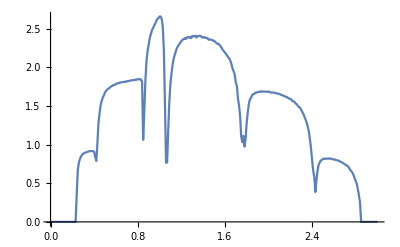

```mathematica
ListPlot[%64,Joined->True]
```

```mathematica
misfit50[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra:=Module[{},lista={RandomSample[{imp9,imp3,imp5,imp1,imp,imp,imp14,imp13,imp1,imp4,imp7,imp,imp,imp10,imp2,imp12,imp6,imp,imp13,imp4,imp6,imp,imp11,imp1,imp,imp5,imp,imp10,imp2,imp,imp14,imp,imp9,imp12,imp6,imp11,imp,imp,imp3,imp,imp10,imp3,imp8,imp9,imp14,imp12,imp,imp8,imp7,imp}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,4,0.01]}];
υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- %64[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- %46[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- %49[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- %52[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- %55[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- %58[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- %61[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%64[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
d50=Table[misfit50[0.5,2.5,0.0],100]
ζ50=N[Mean[Table[Abs[5-Position[d50[[x]],Min[d50[[x]]]][[1,1]]]/5,{x,100}]]]
```

{{0.00886074,0.00450964,0.0025945,0.00174318,0.00143193,0.00140974,0.00155647},{0.00765332,0.00381119,0.00227975,0.00171051,0.00159681,0.00172515,0.00197792},{0.00760769,0.00358861,0.00191231,0.00125267,0.00110893,0.00121911,0.00145511},{0.00744409,0.00353571,0.00202212,0.0015218,0.0015197,0.00175151,0.00208437},{0.00796083,0.00376725,0.00202575,0.00133331,0.00117128,0.00127691,0.00151762},{0.00762758,0.0036852,0.00211993,0.00157025,0.00151201,0.00168756,0.00198401},{0.00815962,0.00390133,0.00216475,0.00148322,0.00131882,0.00142176,0.0016544},{0.00867958,0.00433518,0.00247657,0.00167254,0.00140361,0.00140458,0.00155577},{0.00699616,0.0031927,0.00171851,0.00123475,0.00122296,0.00145406,0.00178685},{0.0078946,0.00375873,0.00205549,0.00136115,0.00118491,0.00127195,0.00149261},{0.00792677,0.00376222,0.00205604,0.00140127,0.00126711,0.0014077,0.00168103},{0.00924485,0.00462228,0.00257912,0.00164794,0.00130137,0.00126648,0.00138663},{0.00736374,0.00344831,0.00183647,0.00123969,0.00116354,0.00133425,0.00162114},{0.00737497,0.00353195,0.00197426,0.00140901,0.00132312,0.00148476,0.00175696},{0.00853695,0.00416343,0.00223319,0.00137182,0.00108031,0.00108374,0.00121248},{0.00737255,0.00347359,0.00194767,0.00143466,0.00141325,0.00163811,0.00196436},{0.0081384,0.00395193,0.00217736,0.00144433,0.00123752,0.0013097,0.00151545},{0.00882529,0.00456068,0.00266429,0.00180663,0.00148156,0.00145498,0.00156357},{0.00872742,0.00434233,0.00243068,0.00159126,0.00132678,0.00132641,0.00148501},{0.00748698,0.00350925,0.00193488,0.00138037,0.00133183,0.00152483,0.00181825},{0.00793065,0.00400939,0.00231531,0.00161922,0.00144067,0.00152881,0.00175784},{0.00831284,0.00413245,0.00235461,0.00161779,0.00140518,0.00148126,0.00169284},{0.00765353,0.00361276,0.00192523,0.00125725,0.00109856,0.00118648,0.00142187},{0.00668262,0.00319603,0.0018744,0.00146294,0.00151251,0.00177387,0.00213027},{0.00711619,0.00329137,0.00181963,0.00131363,0.00128598,0.00148847,0.00178704},{0.00785393,0.00380895,0.00213206,0.00147734,0.00134836,0.00147651,0.00172701},{0.00853665,0.00407088,0.00213596,0.00130931,0.00106324,0.00110648,0.00128519},{0.00825219,0.00397645,0.00219708,0.00147289,0.0012877,0.00137242,0.00159452},{0.00819063,0.00403937,0.00232185,0.00164959,0.00149512,0.00160426,0.00184577},{0.0072136,0.00342837,0.00197115,0.00152517,0.00155756,0.00182694,0.00219268},{0.00749872,0.00363831,0.0021184,0.00158897,0.00152699,0.00170412,0.00198807},{0.00664136,0.00300562,0.00166687,0.00126423,0.00131856,0.00156558,0.00191847},{0.00692899,0.00311971,0.00172067,0.00129758,0.00134081,0.00162516,0.00198526},{0.00841645,0.00415506,0.00235148,0.00161495,0.0014201,0.00152341,0.00175997},{0.00831117,0.00414864,0.00242766,0.00172119,0.00155683,0.00164014,0.00187754},{0.00863132,0.00432793,0.00246926,0.00165897,0.00139426,0.00141782,0.00158623},{0.00818099,0.00395427,0.00215668,0.00141361,0.00119996,0.00127201,0.00147957},{0.00765779,0.00372739,0.00208808,0.00142768,0.00125999,0.00134034,0.00153912},{0.0075648,0.00360413,0.00199768,0.00136192,0.00123952,0.00136759,0.00162205},{0.00801454,0.00376524,0.00199863,0.00129406,0.00113181,0.00124976,0.00148899},{0.00775285,0.00372014,0.00200236,0.00131494,0.0011399,0.00123364,0.00143954},{0.00832138,0.00400961,0.00215306,0.00134608,0.00108476,0.00109857,0.00124631},{0.00777263,0.00374939,0.00208014,0.00142365,0.00126197,0.00137085,0.00161359},{0.00799514,0.00379485,0.00206531,0.00136908,0.00118745,0.00128131,0.00149617},{0.00751434,0.00363971,0.00204052,0.00143232,0.00132176,0.00146045,0.00171217},{0.00764169,0.00370833,0.00214862,0.00158878,0.00151747,0.00169758,0.00198419},{0.00839618,0.00405197,0.00219555,0.00140731,0.00118961,0.00124251,0.00143973},{0.00724374,0.00336971,0.00181503,0.00125826,0.00121041,0.00141634,0.0017363},{0.00785658,0.00384279,0.00218151,0.001519,0.00136076,0.00145608,0.00166698},{0.00827546,0.004063,0.0022919,0.00155322,0.00132617,0.00139112,0.00158228},{0.00803108,0.00392516,0.00219147,0.00149041,0.00130842,0.00138452,0.00159683},{0.00831285,0.00411266,0.00234427,0.00160435,0.00140562,0.00144988,0.0016351},{0.0074074,0.0035415,0.0020319,0.00150187,0.0014563,0.0016483,0.00195681},{0.00708282,0.00318407,0.00169227,0.00118966,0.00119006,0.00142449,0.00175652},{0.00760768,0.00362565,0.00201964,0.00142064,0.00133397,0.00149287,0.00175471},{0.00672343,0.00298908,0.00161749,0.00119484,0.00122701,0.00147475,0.00182436},{0.00883718,0.00445409,0.00253352,0.001676,0.00136467,0.00133904,0.0014456},{0.00831471,0.00412631,0.00232982,0.00155854,0.00130738,0.00133384,0.0015063},{0.00781271,0.00366602,0.00195178,0.00128168,0.00114648,0.00126586,0.00151522},{0.00772309,0.00375614,0.00212873,0.00150058,0.00136253,0.00147842,0.00170609},{0.00817344,0.00391714,0.00214275,0.00142838,0.00124905,0.00134471,0.00156713},{0.00712491,0.00332639,0.00179675,0.00125065,0.00118687,0.00135776,0.00163508},{0.00742293,0.00371755,0.00224031,0.00171293,0.00164071,0.00181429,0.00208757},{0.00977525,0.0050755,0.00292246,0.00189524,0.0014698,0.00136068,0.00140707},{0.00690224,0.00318175,0.00173379,0.00125259,0.0012431,0.00145896,0.00176832},{0.00716157,0.00337237,0.00188064,0.00137309,0.00133944,0.00154264,0.00184044},{0.00766111,0.00371703,0.00213076,0.00154193,0.00144079,0.00159177,0.00186997},{0.00785418,0.0038291,0.00215217,0.00148921,0.00134325,0.00145132,0.00168819},{0.00767927,0.00361922,0.00193074,0.00125111,0.00108801,0.00117712,0.00140782},{0.00711163,0.00322622,0.00172107,0.00122513,0.0012189,0.00144302,0.00177502},{0.00791741,0.00371284,0.00203466,0.00138537,0.00126073,0.00139614,0.00164653},{0.00703491,0.00323535,0.0017582,0.00126297,0.00124104,0.00143931,0.00174746},{0.00836576,0.00404569,0.00219969,0.00142977,0.001218,0.00127023,0.00146347},{0.00766653,0.00363412,0.0020057,0.00138208,0.00125321,0.00137297,0.00160761},{0.00838935,0.00418538,0.00236554,0.00159384,0.00135435,0.00139698,0.00157758},{0.00797731,0.00399164,0.00233109,0.00169494,0.00157019,0.00168151,0.00191984},{0.00767999,0.0036091,0.00199043,0.00139161,0.00129768,0.0014526,0.00173229},{0.00823988,0.00407557,0.0023095,0.00157359,0.00138248,0.00146103,0.00167599},{0.00738414,0.00335889,0.00176686,0.00117444,0.00107701,0.00123887,0.0015039},{0.00669871,0.00304073,0.00165184,0.0012031,0.00121737,0.00144889,0.00177958},{0.00789901,0.00365859,0.00192562,0.00125223,0.00110422,0.00121854,0.00146782},{0.00778356,0.0040037,0.0024509,0.00187484,0.00178376,0.00194147,0.00222145},{0.00802887,0.00380945,0.00203717,0.00133283,0.00116152,0.00126842,0.00149607},{0.00908951,0.00455042,0.00251698,0.00156619,0.00119787,0.00112603,0.00119767},{0.00848645,0.00421199,0.00241123,0.00164693,0.00141054,0.00144767,0.00162252},{0.00928218,0.00468999,0.002627,0.00168845,0.00132307,0.00126356,0.00136139},{0.00792863,0.00385925,0.00213768,0.00143641,0.00125526,0.00132026,0.0015164},{0.00680378,0.00325862,0.00197513,0.00162255,0.00170772,0.00200795,0.00238662},{0.00836522,0.00405849,0.00229575,0.00156643,0.00137245,0.0014445,0.00163692},{0.00627343,0.00276148,0.00152221,0.00121042,0.00134767,0.00169701,0.00213691},{0.00723265,0.003283,0.00169906,0.00113308,0.00108046,0.00127257,0.00157126},{0.0080845,0.00403192,0.00234414,0.00166886,0.00148965,0.00157875,0.0018011},{0.00772729,0.00373874,0.0020795,0.00140953,0.00125353,0.00134614,0.00156342},{0.00831443,0.00415905,0.00240837,0.00169442,0.00150486,0.00158608,0.00180123},{0.0080682,0.00389665,0.00215216,0.00144131,0.00125678,0.00132777,0.00154441},{0.00871811,0.00431383,0.0024063,0.00157689,0.00129213,0.00130278,0.00145972},{0.00784791,0.00377521,0.00207396,0.00141861,0.00127246,0.00139266,0.00164788},{0.00830072,0.00407072,0.00225165,0.00148149,0.00125894,0.00132445,0.00153336},{0.00814272,0.00404944,0.00229497,0.00155258,0.00132623,0.00137142,0.00155871},{0.00798244,0.00388981,0.00218716,0.00149552,0.00131243,0.00138893,0.00157688}}

0.034

```mathematica
misfit4[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra:=Module[{},lista={RandomSample[{imp1,imp7,imp,imp14(*,imp,imp4,imp12,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp11,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp12,imp5,imp6,imp,imp,imp,imp4,imp,imp9,imp,imp,imp8,imp2,imp2,imp7,imp,imp1,imp10,imp,imp6,imp,imp13*)}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,4}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,4,0.01]}];
υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/2imp/2imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/3imp/3imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/4imp/4imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/5imp/5imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/6imp/6imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/7imp/7imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/4unitcells/8imp/8imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%64[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
d4=Table[misfit4[0.5,1.5,0.7],100]
ζ4=N[Mean[Table[Abs[2-Position[d4[[x]],Min[d4[[x]]]][[1,1]]]/2,{x,100}]]]
```

{{0.000125103,0.0000953846,0.00030358,0.00067902,0.00119177,0.00188015,0.00260226},{0.000914702,0.000615319,0.000660948,0.000852577,0.00128296,0.00190573,0.00258044},{0.000324479,0.000188513,0.00036649,0.00069889,0.0012324,0.00196543,0.00272113},{0.000650386,0.000374406,0.000390102,0.000619509,0.000983248,0.00153343,0.0021356},{0.000496147,0.00016694,0.000127346,0.000289768,0.000622943,0.00115261,0.00173116},{0.000733554,0.000420595,0.000404833,0.000593515,0.000933355,0.00145199,0.00203615},{0.000347773,0.000171308,0.000275576,0.000553423,0.00101346,0.00165736,0.00234287},{0.000316251,0.0000948566,0.000172235,0.000424337,0.000863668,0.00149227,0.00217041},{0.00037256,0.000256076,0.00042086,0.000740675,0.00124893,0.0019452,0.00267417},{0.000518162,0.000267077,0.000272625,0.000488036,0.000844117,0.00139221,0.00199511},{0.000655659,0.000411932,0.000509865,0.000758626,0.00122581,0.00189888,0.00261227},{0.000191473,0.0000863877,0.000240406,0.000574572,0.00104562,0.00170283,0.00239806},{0.000844707,0.000582242,0.00063259,0.000845138,0.00128613,0.00192182,0.00258708},{0.000831054,0.000533055,0.000580669,0.000778517,0.00121594,0.0018457,0.00252376},{0.000655776,0.000263831,0.000201918,0.000323672,0.000659716,0.00118455,0.00177097},{0.000147398,0.000145766,0.000384808,0.000801675,0.00135019,0.00207549,0.00283781},{0.000631966,0.000421903,0.0005155,0.000763598,0.00122358,0.00186856,0.00254797},{0.00108652,0.000903547,0.000926312,0.00118688,0.00151813,0.00201697,0.00258409},{0.000639138,0.000283605,0.000248368,0.000386311,0.000740905,0.00127855,0.001871},{0.000626593,0.000372577,0.000433811,0.000679671,0.00110288,0.00170085,0.00236469},{0.000305694,0.000120958,0.000227199,0.000505339,0.00096218,0.00161383,0.0023038},{0.000318019,0.000165059,0.000294571,0.000585751,0.00105703,0.00171288,0.00240892},{0.00070387,0.000339717,0.000314559,0.000487011,0.000849853,0.00140985,0.00202802},{0.000246582,0.0000865152,0.000181941,0.00046693,0.000884765,0.00147947,0.00213102},{0.000189854,0.0000791258,0.000190378,0.000484839,0.000905139,0.00150306,0.00214957},{0.000106039,0.000128429,0.000377183,0.000784854,0.0013263,0.00204166,0.00279245},{0.000258105,0.000107094,0.000197661,0.000479752,0.000893019,0.0014837,0.00212943},{0.00119626,0.000873067,0.000899256,0.00106986,0.00149529,0.00210946,0.00277452},{0.000936553,0.000685614,0.000768924,0.000995865,0.00145495,0.00211198,0.00280317},{0.000182907,0.000103577,0.000275743,0.000625686,0.00111639,0.00179015,0.00249789},{0.00060409,0.000339782,0.000386882,0.00059374,0.00102278,0.00164124,0.00230073},{0.000710453,0.000500074,0.000589646,0.000831959,0.00127479,0.00189707,0.00257619},{0.0012805,0.00116566,0.00124093,0.00154399,0.00191778,0.00245364,0.00305398},{0.000176675,0.0000800287,0.000218934,0.000537378,0.000990886,0.00162307,0.00229657},{0.00027281,0.000162409,0.000357268,0.000716925,0.00125888,0.00199738,0.00275829},{0.00121342,0.000895075,0.000933311,0.00110484,0.00154056,0.00216191,0.00283871},{0.000332878,0.000170525,0.000283064,0.000576885,0.00102413,0.00164857,0.00232498},{0.000637274,0.000405832,0.000486352,0.000718726,0.00117012,0.00181044,0.00248676},{0.000544612,0.000314155,0.000392869,0.000654887,0.00108613,0.00170337,0.00237178},{0.000187606,0.0000766852,0.000199221,0.000503538,0.00093896,0.00154901,0.00221299},{0.000147414,0.00011941,0.000309876,0.000664978,0.00114775,0.00180863,0.00250465},{0.000429566,0.000324109,0.00049814,0.000828958,0.0013525,0.00206847,0.00281058},{0.00018516,0.000143665,0.000350842,0.000732755,0.0012598,0.00197374,0.00271501},{0.000176643,0.000110864,0.000303276,0.000674603,0.00118467,0.00187334,0.00259741},{0.000867755,0.000580177,0.000631156,0.000835404,0.00126858,0.00188754,0.00256008},{0.000821551,0.000564804,0.000613454,0.000813179,0.0012368,0.0018442,0.00250257},{0.00019646,0.000113339,0.000291151,0.000648457,0.00114186,0.00181792,0.00252952},{0.000377219,0.000168244,0.000256953,0.000512707,0.000958639,0.00159746,0.00227838},{0.000520887,0.000280246,0.000297428,0.000511217,0.00086773,0.00140347,0.00199276},{0.000515953,0.000225202,0.000219901,0.00039165,0.000756987,0.00130283,0.00190123},{0.000575107,0.00026652,0.000214201,0.000353464,0.000659875,0.00113422,0.0016727},{0.000376454,0.000278634,0.00044281,0.000798341,0.00127939,0.00194261,0.00266034},{0.000121259,0.0000832983,0.000295766,0.000672315,0.00119327,0.00190702,0.00264726},{0.000118688,0.000105135,0.000330231,0.000728136,0.001257,0.00196888,0.00271545},{0.000374231,0.000222666,0.000357435,0.000656088,0.00112609,0.00177852,0.00248203},{0.000332011,0.000174775,0.000316827,0.00061551,0.00110502,0.0017821,0.00249503},{0.000460616,0.000260972,0.000325081,0.000561842,0.000965807,0.00155361,0.0021817},{0.000162042,0.000130491,0.000350385,0.000740913,0.00127308,0.00198977,0.00272803},{0.00040188,0.000170941,0.000240618,0.000478315,0.000912074,0.00153518,0.00220517},{0.00013145,0.000128374,0.000373838,0.000792841,0.00134603,0.00208487,0.00285186},{0.000390307,0.000160048,0.000232687,0.000481585,0.000920429,0.00155541,0.00222959},{0.000813123,0.000443257,0.000432446,0.00061744,0.00100371,0.00158487,0.00223349},{0.000505884,0.000270622,0.000363127,0.000642183,0.0010963,0.00174573,0.00245058},{0.000679583,0.000409142,0.000401725,0.000594046,0.000939731,0.00145876,0.0020567},{0.000655899,0.000273769,0.000206402,0.000337795,0.000658455,0.00117551,0.00174582},{0.000516511,0.000246604,0.000254065,0.000464158,0.000836959,0.00139317,0.00198999},{0.000356137,0.000145644,0.00023592,0.000502739,0.000957115,0.00160958,0.00229636},{0.000128402,0.0000763294,0.000256946,0.000614291,0.00110011,0.00175726,0.00245663},{0.000516656,0.000233387,0.000187196,0.000336421,0.000625892,0.00109603,0.00162133},{0.000367095,0.000147138,0.000227615,0.00048118,0.000919997,0.00154356,0.00221627},{0.000678817,0.00044087,0.000529686,0.000771213,0.00123918,0.00190066,0.00260338},{0.00048144,0.00026632,0.000287187,0.000498396,0.000841798,0.00136002,0.00192904},{0.000501862,0.000245613,0.000246708,0.000448568,0.000793855,0.00132825,0.0019172},{0.000399965,0.000236671,0.000311628,0.000577688,0.000978163,0.00156311,0.00218198},{0.000474225,0.000183372,0.000150188,0.000322449,0.000649168,0.0011513,0.00171628},{0.000583569,0.000266881,0.000270284,0.000442589,0.000825139,0.00139553,0.00201268},{0.000425102,0.000120133,0.000112665,0.000286966,0.000644859,0.00119273,0.00180048},{0.000208147,0.000073976,0.000176728,0.000466593,0.000887712,0.00148133,0.00212999},{0.000401264,0.000173177,0.000197369,0.0004033,0.000758848,0.00128714,0.00188057},{0.000517666,0.000256159,0.00026188,0.000469239,0.000824576,0.00134787,0.00193909},{0.000863229,0.000552179,0.000548654,0.000708202,0.00109174,0.00166148,0.00228019},{0.000388879,0.000186309,0.000217396,0.000435816,0.000791177,0.00132228,0.00190174},{0.00056393,0.00041424,0.000573825,0.000878326,0.00139484,0.00211062,0.00285555},{0.000220315,0.000133356,0.000293446,0.000627308,0.0011013,0.0017516,0.00244763},{0.000813248,0.000727314,0.000815674,0.00113003,0.00150486,0.00204596,0.00263708},{0.000138168,0.0000774683,0.000266882,0.000632699,0.00112859,0.00180603,0.00251953},{0.000261206,0.000105532,0.000213093,0.000512163,0.00094832,0.00157286,0.00223827},{0.000281951,0.000132531,0.000257255,0.000569295,0.00104364,0.00170688,0.00241045},{0.000978376,0.000620702,0.000592728,0.000753402,0.00111349,0.00165697,0.00228363},{0.000793072,0.000518558,0.000593785,0.000819029,0.00128691,0.00194661,0.00265535},{0.000563588,0.000228884,0.000207665,0.000360785,0.000710743,0.00125435,0.00185368},{0.000641569,0.00040316,0.000496819,0.000748752,0.00122327,0.00188815,0.0025925},{0.000556094,0.000284186,0.000338173,0.000577864,0.00102136,0.00165597,0.00234084},{0.000848905,0.000555501,0.000595917,0.000799245,0.00123297,0.0018487,0.00252035},{0.000389234,0.000171117,0.000258845,0.000534074,0.000969827,0.0016031,0.00227759},{0.00061808,0.000349449,0.000408191,0.000636206,0.00106419,0.00169292,0.00237552},{0.000574383,0.000291124,0.000335429,0.000538905,0.000965933,0.00158077,0.00224658},{0.000603274,0.000233146,0.000172741,0.000306741,0.000616179,0.00111802,0.00169603},{0.000971194,0.000836181,0.000860046,0.0010881,0.00139037,0.00184122,0.00236648},{0.000704569,0.000319582,0.000286396,0.000447457,0.00081063,0.00136937,0.00198879}}

0.095

```mathematica
Tally[Table[Abs[Position[d4[[x]],Min[d4[[x]]]][[1,1]]],{x,100}]]
```

{{2,81},{3,18},{1,1}}

```mathematica
N[5/(14*8)]
```

0.0446429

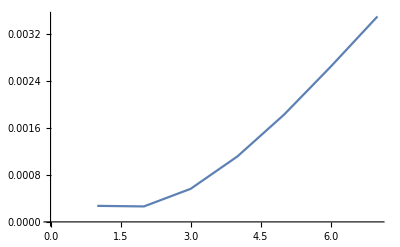

```mathematica
ListLinePlot[d8[[1]]]
```

```mathematica
Table[Abs[4-Position[d8[[x]],Min[d8[[x]]]][[1,1]]]/4,{x,100}]
```

{1/2,1/2,3/4,1/2,1/2,1/2,1/2,1/4,1/2,3/4,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,3/4,1/2,1/2,1/2,1/2,3/4,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/4,1/2,1/4,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
Table[{x,N[x/(14*8)]},{x,10}]
```

{{1,0.00892857},{2,0.0178571},{3,0.0267857},{4,0.0357143},{5,0.0446429},{6,0.0535714},{7,0.0625},{8,0.0714286},{9,0.0803571},{10,0.0892857}}

```mathematica
l={{4,ζ4},{20,0.056},{50,ζ50-0.010},{80,0.005},{100,0.00},{110,0},{120,0},{150,0}}
```

{{4,0.095},{20,0.056},{50,0.024},{80,0.005},{100,0.},{110,0},{120,0},{150,0}}

```mathematica
Interpolation[l]
```

InterpolatingFunction[…]

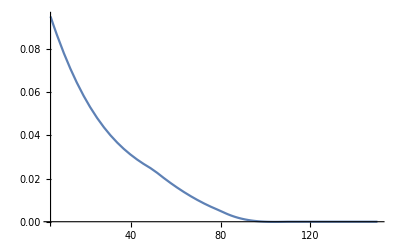

```mathematica
Plot[%204[x],{x,4.,150.}]
```

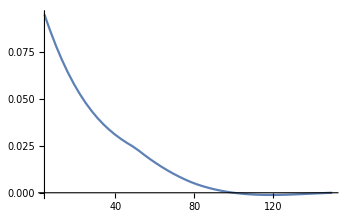

```mathematica
Plot[InterpolatingFunction[{{4.,150.}},{5,7,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{4.,20.,50.,80.,100.,150.}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6},{0.095,0.056,0.024,0.005,0.,0.}},{Automatic}][x],{x,4.,150.}]
```

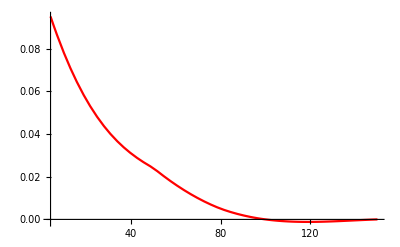

```mathematica
Plot[InterpolatingFunction[{{4.,150.}},{5,7,0,{6},{4},0,0,0,0,Automatic,{},{},False},{{4.,20.,50.,80.,100.,150.}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6},{0.095,0.056,0.024,0.005,0.,0.}},{Automatic}][x],{x,4.,150.},PlotStyle->{Red}]
```

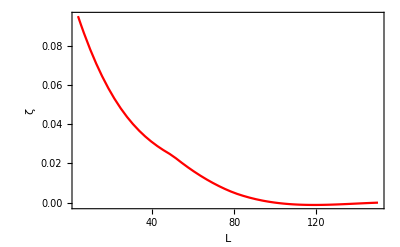

```mathematica
Show[%209,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{HoldForm[ζ],None},{HoldForm[L],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Frame->True(*Epilog->{Text[Style["(b)","Times New Roman",18],{0.2,2.8}]},*)]
```

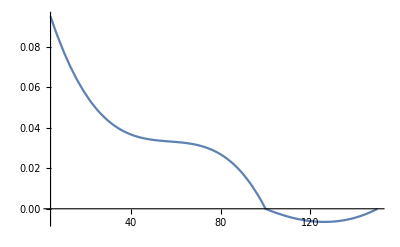

```mathematica
Plot[InterpolatingFunction[{{4.,150.}},{5,7,0,{5},{4},0,0,0,0,Automatic,{},{},False},{{4.,20.,50.,100.,150.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{0.095,0.056,0.034,0.,0.}},{Automatic}][x],{x,4.,150.}]
```

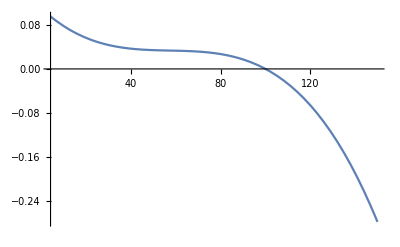

```mathematica
Plot[InterpolatingFunction[{{4.,100.}},{5,7,0,{4},{4},0,0,0,0,Automatic,{},{},False},{{4.,20.,50.,100.}},{Developer`PackedArrayForm,{0,1,2,3,4},{0.095,0.056,0.034,0.}},{Automatic}][x],{x,4.,150.}]
```

InterpolatingFunction::dmval: Input value {1.00304} lies outside the range of data in the interpolating function. Extrapolation will be used.

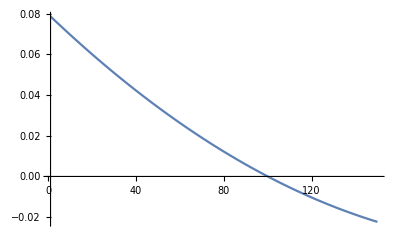

```mathematica
Plot[InterpolatingFunction[{{20.,100.}},{5,7,0,{3},{3},0,0,0,0,Automatic,{},{},False},{{20.,50.,100.}},{Developer`PackedArrayForm,{0,1,2,3},{0.06,0.034,0.}},{Automatic}][x],{x,1.,150.}]
```

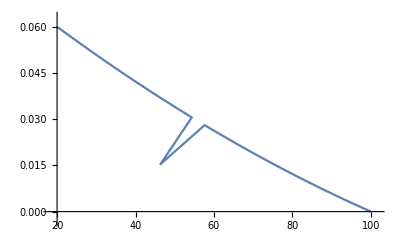

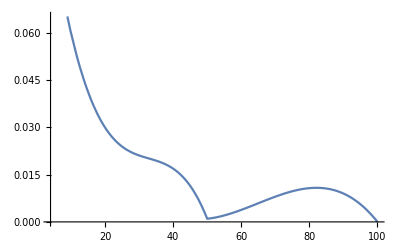

```mathematica
Plot[InterpolatingFunction[{{4.,100.}},{5,7,0,{5},{4},0,0,0,0,Automatic,{},{},False},{{4.,8.,20.,50.,100.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{0.095,0.07,0.03,0.001,0.}},{Automatic}][x],{x,4.,100.}]
```

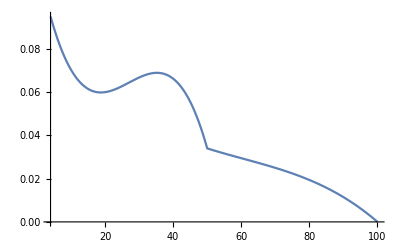

```mathematica
Plot[%170[x],{x,4.,100.}]
```

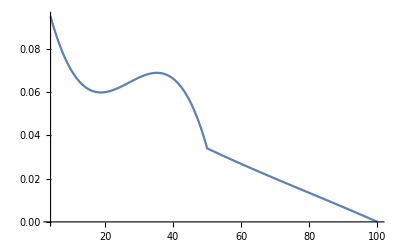

```mathematica
Plot[%167[x],{x,4.,100.}]
```

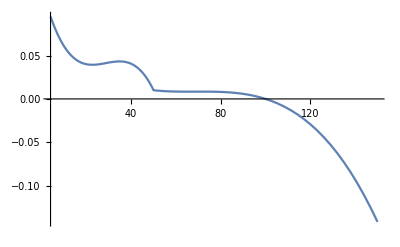

```mathematica
Plot[InterpolatingFunction[{{4.,100.}},{5,7,0,{5},{4},0,0,0,0,Automatic,{},{},False},{{4.,8.,20.,50.,100.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{0.095,0.07,0.04,0.01,0.}},{Automatic}][x],{x,4.,150.}]
```

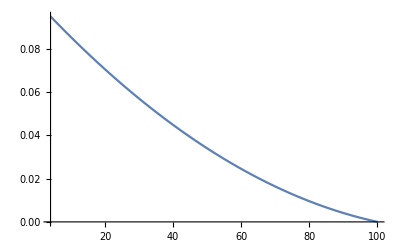

```mathematica
Plot[InterpolatingFunction[{{0.,100.}},{5,7,0,{3},{3},0,0,0,0,Automatic,{},{},False},{{4.,50.,100.}},{Developer`PackedArrayForm,{0,1,2,3},{0.095,0.034,0.}},{Automatic}][x],{x,4.,100.}]
```

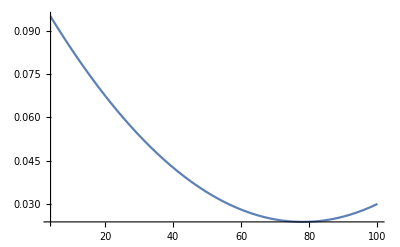

{{1,0.00714286},{2,0.0142857},{3,0.0214286},{4,0.0285714},{5,0.0357143},{6,0.0428571},{7,0.05},{8,0.0571429},{9,0.0642857},{10,0.0714286},{11,0.0785714},{12,0.0857143},{13,0.0928571},{14,0.1},{15,0.107143},{16,0.114286},{17,0.121429},{18,0.128571},{19,0.135714},{20,0.142857}}

```mathematica
Plot[InterpolatingFunction[{{4.,100.}},{5,7,0,{3},{3},0,0,0,0,Automatic,{},{},False},{{4.,50.,100.}},{Developer`PackedArrayForm,{0,1,2,3},{0.095,0.034,0.03}},{Automatic}][x],{x,4.,100.}]
```

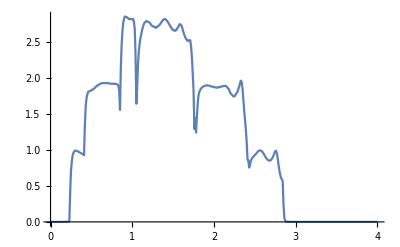

```mathematica
ListLinePlot[ Import["/home/shardulmukim/PhD/fwi/7AGNR/8_unit_cells/2imp4.csv"]]
```

```mathematica
m[ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra:=Module[{},lista={{imp13,imp,imp1,imp,imp2,imp12,imp,imp6,imp,imp1,imp12,imp9,imp6,imp4,imp10,imp,imp,imp6,imp4,imp,imp3,imp8,imp,imp10,imp14,imp13,imp14,imp5,imp,imp,imp11,imp,imp,imp7,imp,imp13,imp8,imp2,imp3,imp7,imp3,imp,imp12,imp,imp,imp1,imp,imp5,imp12,imp,imp11,imp2,imp,imp,imp,imp,imp5,imp14,imp11,imp,imp,imp,imp,imp5,imp9,imp,imp4,imp,imp7,imp14,imp3,imp,imp,imp,imp,imp,imp7,imp,imp,imp8,imp,imp,imp2,imp8,imp,imp,imp6,imp,imp13,imp9,imp9,imp1,imp,imp4,imp,imp11,imp,imp,imp10,imp10}};
b=Table[{ω,Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]]},{ω,Range[0,4,0.04]}];
b];
tra]
```

```mathematica
m[0.5]
```

$Aborted